# Parametric Surface Design for Static Solar Concentration : Enhancing Plastic Waste Pyrolysis in Sustainable Housing Mathematics and Computers in Simulation

This work develops a mathematical framework for the design of static parabolic solar concentrators with purely parametric geometries, aimed at replacing mechanically tracked systems . The central problem is to translate the apparent solar motion into a continuous parabolic surface whose focal line evolves consistently with the sun' s trajectory . We formulate the astronomical parameters (solar declination, hour angle, azimuth-- elevation) and show how each parabola, defined in its local plane, is rotated and assembled into a complete surface through parametric transformations . To ensure smoothness and predictable reflection properties, the resulting point cloud is interpolated using spline - based methods that guarantee C^2 continuity, enabling reliable computation of tangents and normals . Practical implementation is achieved through an embedded device that verifies point placement during construction, bridging theoretical design with reproducible fabrication . While the broader motivation of this study is to address plastic waste through solar pyrolysis, the focus here is on the mathematical formulation that underpins the geometry and interpolation techniques necessary for building resilient, low - cost, and efficient static concentrators .

## Solar geometry : latitude, day angle and solar declination

#### Definition of site latitude

Site latitude in radians.The reference location considered in this model is set to 37 degrees north.This parameter defines the observer position on Earth and directly affects the solar trajectory and all derived solar angles.

```mathematica
latitude=37 Degree;
```

#### Day angle and solar declination (Spencer model)

Daily angle beta(dn),also known as the day angle.This variable maps the day of the year (dn) into a periodic angular scale,representing the Earth's orbit around the Sun.

```mathematica
beta[dn_]:=2 Pi (dn-1)/365;
```

#### Solar declination delta (dn) computed using Spencer' s Fourier - series approximation .

This analytical expression provides a high-accuracy representation of the seasonal variation of the solar declination angle.The declination angle defines the tilt between the Earth's equatorial plane and the Sun-Earth direction,and it is a key input for computing solar elevation and azimuth angles.

```mathematica
delta[dn_]:=0.006918-0.399912 Cos[beta[dn]]+0.070257 Sin[beta[dn]]-0.006758 Cos[2 beta[dn]]+0.000907 Sin[2 beta[dn]]-0.002697 Cos[3 beta[dn]]+0.00148 Sin[3 beta[dn]];
```

#### Visualization of solar declination over the year .

This plot illustrates the seasonal variation of the declination angle,ranging approximately between-23.44° and+23.44°.

```mathematica
Plot[{delta[dd]},{dd,1,365},FrameLabel->{"Day of year (dn)","δ [rad]"},Frame->True,PlotTheme->"Marketing",LabelStyle->Directive[Black,Bold,Large],ImageSize->1000]
```

-Graphics-

## Solar time and solar angles

#### Hour angle and solar time

Hour angle H (in radians) computed from the true solar time (TST,in hours). The hour angle represents the angular displacement of the Sun with respect to the local meridian. It is zero at solar noon,negative in the morning,and positive in the afternoon. The factor 15° per hour corresponds to the Earth's rotation rate.Subtracting 12 centers the system at solar noon.

```mathematica
timeH[TST_]:=15 Degree (TST-12);
```

#### Solar elevation and zenith angles

Solar zenith angle Z (in radians). This is the angle between the local vertical direction and the solar direction. Note:This angle is NOT the solar azimuth.

```mathematica
zenith[dn_,TST_]:=ArcCos[Sin[latitude] Sin[delta[dn]]+Cos[latitude] Cos[delta[dn]] Cos[timeH[TST]]];
```

Solar elevation angle h (in radians). This is the angle between the solar direction and the horizontal plane.

```mathematica
h[dn_,TST_]:=ArcSin[Sin[latitude] Sin[delta[dn]]+Cos[latitude] Cos[delta[dn]] Cos[timeH[TST]]];
```

#### Geometric solar azimuth (model convention)

Solar azimuth in the geometric convention adopted for the mirror model.This is a signed angle in the horizontal xy-plane:-measured from the positive x-axis-counterclockwise-negative in the morning,positive in the afternoon This definition differs from standard solar azimuth formulations,but preserves continuity and is consistent with the geometric construction of the mirror surface.

```mathematica
azimuth[dn_,TST_]:=Module[{sx,sy},
(*Horizontal projection of the solar direction*)
sx=Sin[latitude] Cos[delta[dn]] Cos[timeH[TST]]-Cos[latitude] Sin[delta[dn]];
sy=Cos[delta[dn]] Sin[timeH[TST]];
(*Quadrant-aware angle*)
ArcTan[sx,sy]];
```

#### Consistency check

Example day for validation

```mathematica
dn=160;
```

The zenith angle must satisfy : zenith = Pi/2 - elevation

```mathematica
Plot[{zenith[dn,hora],Pi/2-h[dn,hora]},{hora,9,15},FrameLabel->{"Solar time [h]","Angle [rad]"},Frame->True,PlotTheme->"Marketing",PlotLegends->{"zenith","Pi/2 - elevation"},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000]
```

-Graphics-

## Horizontal projection

This block computes the horizontal projection of the solar direction for a selected day . The resulting curve represents the solar sweep in the xy - plane using the geometric convention adopted in this model. In this convention, the azimuth is not expressed in the standard astronomical reference frame, but as a signed geometric angle measured from the positive x - axis in the counterclockwise direction . This definition is the one used later to generate the parabolic sections and the three - dimensional mirror surface .

#### Horizontal projection of the solar direction.

Horizontal x - component of the solar direction . Cos[h] gives the magnitude of the horizontal projection, while Cos[azimuth] gives its component along the x - axis .

```mathematica
x[dn_,TST_]:=Cos[h[dn,TST]] Cos[azimuth[dn,TST]];
```

Horizontal y-component of the solar direction.Cos[h] gives the magnitude of the horizontal projection,while Sin[azimuth] gives its component along the y-axis.

```mathematica
y[dn_,TST_]:=Cos[h[dn,TST]] Sin[azimuth[dn,TST]];
```

#### Example of daily horizontal sweep.

Example day and facade length used for visualization.

```mathematica
dn=170;
FacadeLength=30;
```

Normalization factor for the lateral excursion over the selected time interval.This avoids using a single endpoint as reference and keeps the sweep scaled to the facade width.

```mathematica
yNorm=Max[Abs@Table[y[dn,hora],{hora,12-3,12+3,0.01}]];
```

Daily horizontal solar sweep in the adopted geometric convention . The x - component is kept in its natural normalized form, whereas the y - component is scaled to the facade width in order to visualize the region where the distributed reactor is placed .

```mathematica
dataXY=Table[{x[dn,hora],(FacadeLength/2) y[dn,hora]/yNorm,0},{hora,12-3,12+3,0.01}];
```

#### 3 D visualization of the horizontal solar path .

Although the curve lies in the plane z=0,ListPointPlot3D is used to maintain consistency with the later 3D representation of the mirror surface and focal trajectory.

```mathematica
horizontalSweep=ListPointPlot3D[dataXY,AxesLabel->{"x [m]","y [m]","z [m]"},PlotLabel->"Horizontal solar sweep in the model reference frame",PlotTheme->"Marketing",LabelStyle->Directive[Black,Bold],AspectRatio->1,ImageSize->1000]
```

-Graphics3D-

## Local parabolic profile driven by solar elevation

This section illustrates how the local parabolic cross - section of the mirror evolves throughout the day as a function of the solar elevation . The purpose of this block is mainly interpretative : through static examples and animations, it helps to understand how each parabola tilts, rises, and descends as the Sun moves from morning to afternoon . In this stage, only the vertical plane (xz - plane) is considered . 

The horizontal azimuthal sweep will be introduced later in the full three - dimensional construction of the mirror surface .

Mirror profile for a fixed day.This section illustrates how each local parabolic cross-section is generated in the vertical plane as a function of solar time.The local profile is controlled by the solar zenith angle,whereas the horizontal azimuthal sweep is introduced later in the full 3D construction of the mirror surface.

Reference day and geometric parameters. Selected day of the year.This example uses day 160,corresponding approximately to early June in a non-leap year.

```mathematica
dn=160;
```

Focal length of the parabolic mirror (in meters).

```mathematica
f=1;
```

#### Local orientation of the parabolic profile .

Local rotation angle of the parabolic section.The profile is oriented according to the solar zenith angle,which defines the inclination of the incoming solar rays in the vertical plane.

```mathematica
thetaLocal[TST_]:=zenith[dn,TST];
```

#### Parametric definition of the parabolic profile :

Local x-coordinate of the rotated parabola.The expression corresponds to a standard parabola rotated by the zenith angle.

```mathematica
xLocal[t_,TST_]:=t Cos[thetaLocal[TST]]-(t^2/(4 f)) Sin[thetaLocal[TST]];
```

Local z - coordinate of the rotated parabola .

```mathematica
zLocal[t_,TST_]:=t Sin[thetaLocal[TST]]+(t^2/(4 f)) Cos[thetaLocal[TST]];
```

#### Focal point associated with the solar elevation

The focal point follows the solar elevation angle.Its position shifts vertically throughout the day as the Sun rises and sets.

```mathematica
fxLocal[TST_]:=-f Cos[h[dn,TST]];
fzLocal[TST_]:=f Sin[h[dn,TST]];
```

#### Static example : single solar time .

Example of the parabolic profile at a fixed solar time.This allows visualizing the geometry of a single mirror section and its corresponding focal point.

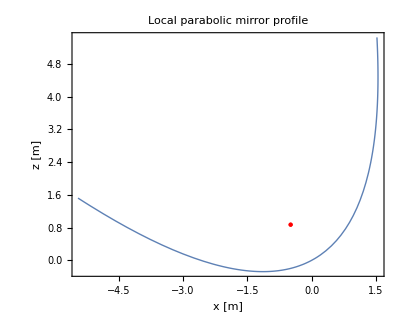

```mathematica
exampleProfile=Show[ParametricPlot[{xLocal[t,10],zLocal[t,10]},{t,-4,4},PlotStyle->Thick,Frame->True,FrameLabel->{"x [m]","z [m]"},PlotLabel->"Local parabolic mirror profile",LabelStyle->Directive[Black,Bold]],ListPlot[{{fxLocal[10],fzLocal[10]}},PlotStyle->{Red,PointSize[Large]}]]
```

Animation of the daily evolution of the parabolic profile. This animation shows how the parabolic profile continuously changes throughout the day.As the solar elevation increases (morning to noon), the parabola tilts upward and its focal point rises. After solar noon,the process reverses: the parabola descends and the focal point lowers.This dynamic behavior is the basis for constructing the full mirror surface as an envelope of time-dependent parabolic sections.

```mathematica
Animate[Show[ParametricPlot[{xLocal[t,TST],zLocal[t,TST]},{t,-4,4},PlotStyle->Thick,Frame->True,FrameLabel->{"x [m]","z [m]"},FrameTicksStyle->Directive[Black,Bold,18],ImageSize->700],ListPlot[{{fxLocal[TST],fzLocal[TST]}},PlotStyle->{Red,PointSize[Large]}]],{TST,9,15,Appearance->"Labeled"},AnimationRunning->False]
```

## Parametric construction of the mirror surface

This section introduces the full parametric construction of the mirror surface . The mirror is generated as a collection of local parabolic sections defined in the vertical plane (xz - plane), which are subsequently positioned in space through rigid transformations . 

Each section is : 
	-oriented according to the solar zenith angle (vertical tilt),
	-rotated according to the geometric solar azimuth (horizontal sweep),
	-translated along the horizontal solar trajectory . 
  
The combination of these operations produces the complete three - dimensional geometry of the mirror as an envelope of time - dependent parabolic profiles .

#### Rigid transformation in 3 D space

Rigid transformation of a 3D point set:-first,a rotation around the z-axis,-then,a translation in the xy-plane.This transformation is essential to correctly place each local parabolic section in the global coordinate system,assigning both its azimuthal orientation and its horizontal position along the solar trajectory.

```mathematica
TransformCurve[points_List,angle_,dx_,dy_]:=Module[{rotationMatrix,rotatedPoints},(*Rotation matrix around the z-axis*)rotationMatrix={{Cos[angle],-Sin[angle],0},{Sin[angle],Cos[angle],0},{0,0,1}};
(*Apply rotation*)
rotatedPoints=(rotationMatrix.#)&/@points;
(*Apply translation in the xy-plane*)
(#+{dx,dy,0})&/@rotatedPoints];
```

#### Local parabolic profile (vertical plane)

Focal length of the parabolic cross-section (in meters)

```mathematica
f=1;
```

Local x - coordinate of the parabolic profile . The parabola is defined in the vertical plane and rotated according to the solar zenith angle, which determines the inclination of the incident solar rays .

```mathematica
xref[dn_,TST_,t_]:=t Cos[zenith[dn,TST]]-(t^2/(4 f)) Sin[zenith[dn,TST]];
```

Local z - coordinate of the parabolic profile .

```mathematica
zref[dn_,TST_,t_]:=t Sin[zenith[dn,TST]]+(t^2/(4 f)) Cos[zenith[dn,TST]];
```

#### Focal trajectory

Horizontal coordinate of the focal point . The focal point shifts horizontally according to the solar elevation .

```mathematica
fx[dn_,TST_]:=-f Cos[h[dn,TST]];
```

Vertical coordinate of the focal point.The focal point rises and descends following the solar elevation.

```mathematica
fz[dn_,TST_]:=f Sin[h[dn,TST]];
```

#### Horizontal solar projection (geometric azimuth)

Horizontal x - component of the solar direction . The projection is defined using the geometric azimuth introduced previously, ensuring consistency with the model reference frame .

```mathematica
x[dn_,TST_]:=Cos[h[dn,TST]] Cos[azimuth[dn,TST]];
```

Horizontal y - component of the solar direction .

```mathematica
y[dn_,TST_]:=Cos[h[dn,TST]] Sin[azimuth[dn,TST]];
```

#### Geometric scaling parameters

Facade length (in meters) . This parameter defines the physical extent of the mirror system in the horizontal direction and is used later to scale the solar sweep .

```mathematica
FacadeLength=30;
```

## Generation of the mirror surface and focal trajectory for selected days

This block defines a reusable function that generates both the mirror surface and the associated focal trajectory for any selected day of the year.The construction is performed by sweeping the true solar time over the operating interval.For each solar time:-a local parabolic section is generated in the xz-plane,-the corresponding focal point is computed,-both are rotated according to the geometric azimuth,-and translated along the horizontal solar sweep.The output is stored as an association with two components:"Surface",containing the collection of transformed parabolic sections,and "Focus",containing the corresponding transformed focal points.This modular construction makes it possible to compare mirror geometries generated for different days under identical sampling conditions.

#### Reusable generator for the mirror surface and focal trajectory

GenerateSurfaceAndFocus[dn] constructs the mirror surface and the corresponding focal trajectory for a given day of the year.
Input:
	- dn:day number of the year Output:
	- an association with two entries:
                                                "Surface"->collection of transformed parabolic sections 
                                                "Focus"->collection of transformed focal points

```mathematica
GenerateSurfaceAndFocus[dn_]:=Module[{j=0,yNormLocal,data,focus},
(*Normalization factor for the lateral displacement over the full operating interval of the selected day.This ensures that the horizontal sweep is consistently scaled.*)
yNormLocal=Max[Abs@Table[y[dn,TST],{TST,12-3,12+3,0.01}]];
(*Sweep the true solar time over the selected operating window.*)
For[TST=12-3,TST<=12+3,TST+=0.05,j=j+1;
(*Initialize storage for the current parabolic section and focal point.*)
data[j]={};
focus[j]={};
(*Generate the local parabolic profile in the xz-plane by sweeping the parabola parameter t.*)
For[i=-600,i<=600,i++,t=i/200;
data[j]=Append[data[j],{xref[dn,TST,t],0,zref[dn,TST,t]}];];
(*Local focal point before the rigid transformation.*)
focus[j]={{fx[dn,TST],0,fz[dn,TST]}};
(*Apply the rigid transformation to the focal point:-rotation by the opposite of the geometric azimuth,-translation along the horizontal solar trajectory.*)
focus[j]=TransformCurve[focus[j],-azimuth[dn,TST],x[dn,TST],FacadeLength/2*y[dn,TST]/yNormLocal];
(*Apply the same rigid transformation to the full parabolic section.*)
data[j]=TransformCurve[data[j],-azimuth[dn,TST],x[dn,TST],FacadeLength/2*y[dn,TST]/yNormLocal];];
(*Return both the mirror surface and the focal trajectory as an association.*)<|"Surface"->Table[data[k],{k,1,j}],"Focus"->Table[focus[k],{k,1,j}]|>];
```

#### Generation of mirror surfaces for two representative summer days

Two representative summer days are considered in order to compare the resulting mirror geometries and focal trajectories.Day 145 is used as a reference summer day.Day 200 is introduced as a nearby operating day to evaluate whether the mirror geometry remains practically unchanged within the selected summer interval.

```mathematica
(*25/May*)
day145=GenerateSurfaceAndFocus[145]; 
(*19/July*)
day200=GenerateSurfaceAndFocus[200];
```

#### Extraction of surfaces and focal trajectories

Mirror surface and focal trajectory for day 145.

```mathematica
SurfacesDay145=day145["Surface"];
ReactorDay145=day145["Focus"];
```

Mirror surface and focal trajectory for day 200.

```mathematica
SurfacesDay200=day200["Surface"];
ReactorDay200=day200["Focus"];
```

At this stage, the mirror surface is represented as a discrete set of transformed parabolic sections . In later steps, this point cloud can be visualized, interpolated, or exported for fabrication and simulation .

#### 3 D visualization of the spatial range for day 145

This block generates a three - dimensional representation that combines :
    -The points defining the surfaces (SurfacesDay145)
    -The points representing the reactor (ReactorDay145) 

 Both geometries are displayed simultaneously to analyze their relative arrangement in space (x, y, z) .

```mathematica
rangoDay145=Show[
(*------------------------------------------------------------*)
(*1. Point cloud of the surfaces (day 145)*)
(*------------------------------------------------------------*)
ListPointPlot3D[SurfacesDay145,
(*Axis labels in physical units*)AxesLabel->{"x [m]","y [m]","z [m]"},(*Label style:black,bold,large size*)LabelStyle->Directive[Black,Bold,Large]],(*------------------------------------------------------------*)
(*2. Point cloud of the reactor (day 145)*)
(*------------------------------------------------------------*)
ListPointPlot3D[ReactorDay145,(*Labels are repeated for visual consistency*)AxesLabel->{"x [m]","y [m]","z [m]"},(*Same typographic style as the surface*)LabelStyle->Directive[Black,Bold,Large]],ImageSize->1000]
```

-Graphics3D-

#### 3 D visualization of the spatial range for day 200

This block generates a three-dimensional representation that combines:
	-The surfaces corresponding to day 200 (SurfacesDay200)
	-The reactor geometry for the same day (ReactorDay200) 

The objective is to visualize both structures within the same coordinate system (x,y,z) in order to analyze their spatial relationship.

```mathematica
rangoDay200=Show[
(*------------------------------------------------------------*)
(*1. Point cloud of the surfaces (day 200)*)
(*------------------------------------------------------------*)
ListPointPlot3D[SurfacesDay200,(*Axis labels with physical units*)AxesLabel->{"x [m]","y [m]","z [m]"},(*Label style:black,bold,large size*)LabelStyle->Directive[Black,Bold,Large]],

(*------------------------------------------------------------*)
(*2. Point cloud of the reactor (day 200)*)
(*------------------------------------------------------------*)
ListPointPlot3D[ReactorDay200,(*Same labels are used for visual consistency*)AxesLabel->{"x [m]","y [m]","z [m]"},(*Same label style as for the surfaces*)LabelStyle->Directive[Black,Bold,Large]],ImageSize->1000]
```

-Graphics3D-

## Quantitative comparison between day 145 and day 200

Visual comparison of the mirror surfaces and focal trajectories corresponding to day 145 and day 200. Both datasets are plotted simultaneously in order to qualitatively assess the overlap between the two geometries.This visualization provides an intuitive confirmation that the surfaces are nearly indistinguishable within the selected summer operating interval.However,visual inspection alone is not sufficient to quantify the differences.For this reason,a detailed pointwise numerical comparison is performed in the following section.

```mathematica
Show[rangoDay145,rangoDay200,ImageSize->1000]
```

-Graphics3D-

#### Quantitative comparison between day 170 and day 176

This block compares the mirror surfaces and focal trajectories obtained for day 145 and day 200. Since both surfaces are generated with the same parameter sampling in solar time and in the local parabola parameter t,a point-to-point comparison can be performed directly.The goal is to quantify how close both parametric surfaces are over the selected summer operating interval.

```mathematica
(*Pointwise Euclidean distances between both mirror surfaces*)
surfacePointDistances=MapThread[EuclideanDistance,{Flatten[SurfacesDay145,1],Flatten[SurfacesDay200,1]}];

(*Pointwise Euclidean distances between both focal trajectories*)
focusPointDistances=MapThread[EuclideanDistance,{Flatten[ReactorDay145,1],Flatten[ReactorDay200,1]}];
```

#### Summary statistics for the geometric comparison

The following quantities summarize the pointwise geometric differences between the two mirror surfaces and between their corresponding focal trajectories.These indicators are computed from the Euclidean distances previously obtained for all matched points.The goal is to quantify,in a compact form,how similar both configurations are.

```mathematica
(*Maximum pointwise deviation on the mirror surface.This is the largest Euclidean distance found between any pair of corresponding surface points.It provides a worst-case estimate of the geometric discrepancy between both surfaces.*)
surfaceMaxError=Max[surfacePointDistances];

(*Mean pointwise deviation on the mirror surface.This is the arithmetic average of all pointwise distances over the full surface.It provides a global estimate of the typical geometric difference between both mirror configurations.*)
surfaceMeanError=Mean[surfacePointDistances];

(*Root-mean-square deviation on the mirror surface.The RMS error gives a measure of the overall discrepancy while assigning greater weight to larger local deviations.This is useful to detect whether the differences are uniformly small or whether a few larger departures dominate the comparison.*)
surfaceRMSError=Sqrt[Mean[surfacePointDistances^2]];

(*Maximum pointwise deviation on the focal trajectory.This is the largest Euclidean distance between any pair of corresponding focal points.It represents the maximum displacement of the focal path between the two compared days.*)
focusMaxError=Max[focusPointDistances];

(*Mean pointwise deviation on the focal trajectory.This value represents the average displacement of the focal trajectory over the full daily operating interval.*)
focusMeanError=Mean[focusPointDistances];

(*Root-mean-square deviation on the focal trajectory.As in the case of the surface,this quantity emphasizes larger local departures and provides an overall measure of the focal-path discrepancy.*)
focusRMSError=Sqrt[Mean[focusPointDistances^2]];

(*Collect all summary indicators in a single association for convenient inspection and reporting.These values can be directly quoted in the manuscript in order to demonstrate that the geometric differences between both days remain negligible.*)
comparisonSummary={"Surface max error [m]"->surfaceMaxError,"Surface mean error [m]"->surfaceMeanError,"Surface RMS error [m]"->surfaceRMSError,"Focus max error [m]"->focusMaxError,"Focus mean error [m]"->focusMeanError,"Focus RMS error [m]"->focusRMSError}
```

{Surface max error [m]→0.0209595,Surface mean error [m]→0.00803287,Surface RMS error [m]→0.00905618,Focus max error [m]→0.00151178,Focus mean error [m]→0.00116575,Focus RMS error [m]→0.00117884}

#### Relative geometric error with respect to the characteristic system size

In order to assess the significance of the geometric discrepancies, the previously computed absolute errors are normalized by the characteristic length of the system,given here by FacadeLength.This allows the errors to be interpreted in a dimensionless form,making it easier to evaluate whether they are negligible in practical terms.

Relative maximum deviation on the mirror surface.This value represents the worst-case geometric error normalized by the overall size of the system.It provides a scale-independent measure of the largest local deviation.

Relative RMS deviation on the mirror surface.This quantity gives a global,normalized measure of the overall surface discrepancy,with increased sensitivity to larger local deviations.

Relative maximum deviation on the focal trajectory.This indicates the maximum displacement of the focal path relative to the system size,allowing direct assessment of its practical impact.

```mathematica
(*Relative RMS deviation on the focal trajectory.This provides a normalized measure of the overall variation in the focal trajectory across the operating interval.*)relativeComparisonSummary={"Surface max error / FacadeLength"->surfaceMaxError/FacadeLength,"Surface RMS error / FacadeLength"->surfaceRMSError/FacadeLength,"Focus max error / FacadeLength"->focusMaxError/FacadeLength,"Focus RMS error / FacadeLength"->focusRMSError/FacadeLength}
```

{Surface max error / FacadeLength→0.00069865,Surface RMS error / FacadeLength→0.000301873,Focus max error / FacadeLength→0.0000503927,Focus RMS error / FacadeLength→0.0000392947}

#### Statistical distribution of pointwise surface deviations

This histogram represents the statistical distribution of the pointwise Euclidean distances between corresponding surface points for the two analyzed days (day 145 and day 200).Each value in surfacePointDistances corresponds to the local geometric difference between two matched points on the parametric mirror surfaces.The purpose of this visualization is:-to assess whether the discrepancies are uniformly small,-to detect the presence of outliers or localized deviations,-and to confirm that the majority of the surface points exhibit negligible differences.A narrow distribution concentrated near zero indicates a high degree of geometric invariance between both surfaces,which is consistent with the robustness of the parametric formulation with respect to small variations in solar parameters.

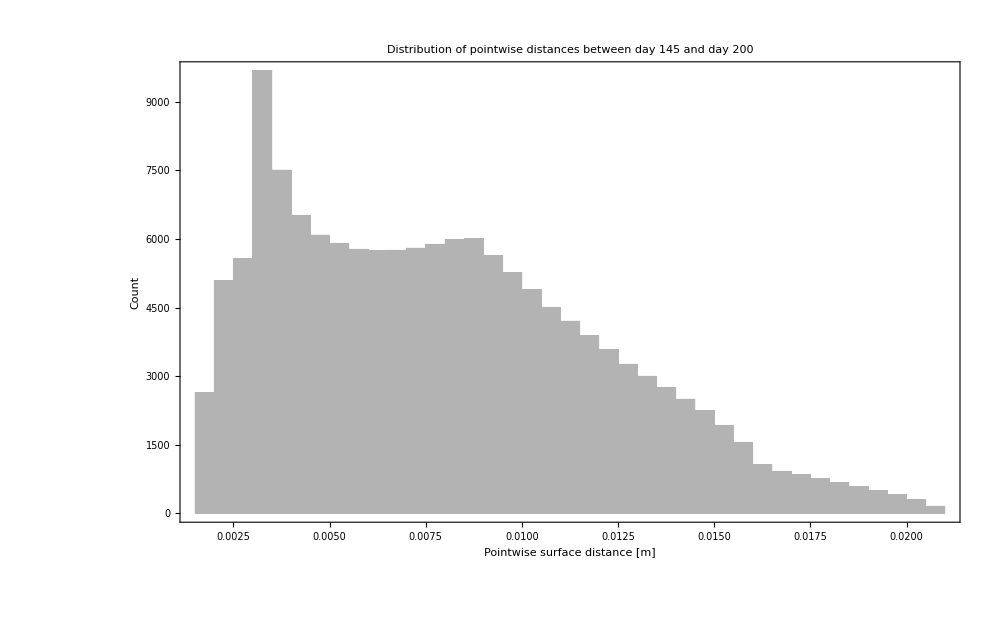

```mathematica
Histogram[surfacePointDistances,40,(*number of bins to resolve the distribution with sufficient detail*)Frame->True,FrameLabel->{Style["Pointwise surface distance [m]",20,Black,Bold],(*horizontal axis:geometric deviation*)Style["Count",20,Black,Bold] 
  (*vertical axis:number of points in each bin*)},PlotLabel->Style["Distribution of pointwise distances between day 145 and day 200",24,Black,Bold],PlotTheme->"Monochrome",(*clean visualization for publication*)LabelStyle->Directive[Black,Bold] (*consistent formatting*),FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000]
```

#### Histogram of pointwise distances between focal points (day 145 vs 200)

This block represents the distribution of distances between :
	-the focal points of day 145
	- the corresponding focal points of day 200 It is assumed that focusPointDistances is a list of numerical values, where each element represents the distance between two matched focal points at the same time instant or section .

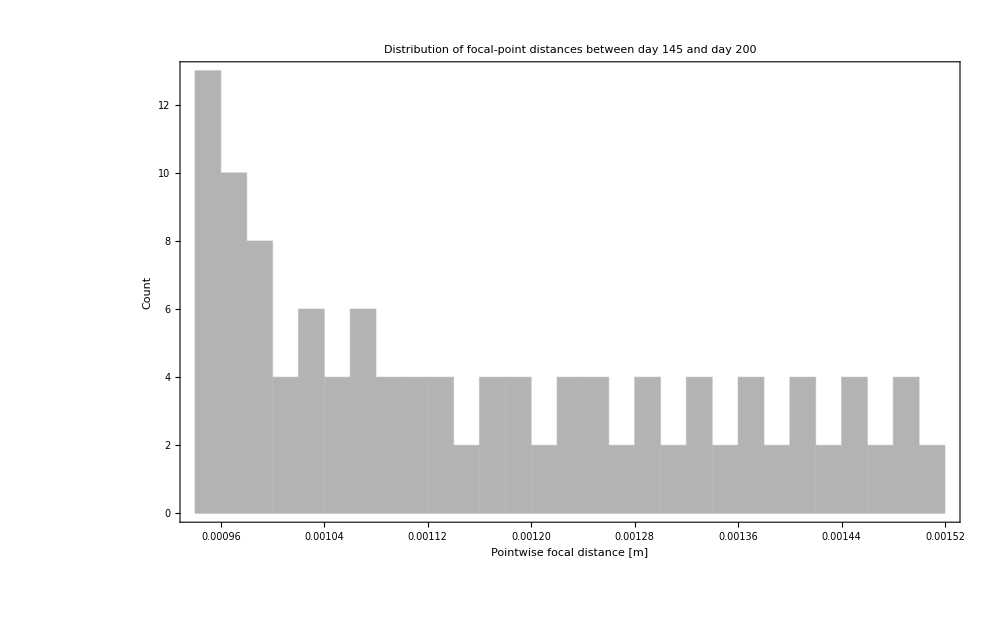

```mathematica
Histogram[focusPointDistances,(*list of pointwise distances*)30,(*number of histogram bins*)
(*--------------------------------------------------------------*)
(*Display options*)
(*--------------------------------------------------------------*)
Frame->True,(*use full frame instead of standard axes*)FrameLabel->{Style["Pointwise focal distance [m]",20,Black,Bold],Style["Count",20,Black,Bold]},(*Plot title:describes the distribution of focal-point distances*)PlotLabel->Style["Distribution of focal-point distances between day 145 and day 200",24,Black,Bold],(*Monochrome visual style (useful for publications)*)PlotTheme->"Monochrome",(*Label typography*)LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000]
```

#### Section - by - section distances : one mean value is obtained for each TST

sectionErrors will store, for each section k, a single discrepancy measure between the surfaces of day 145 and day 200. The idea is :
    	1. Take section k from SurfacesDay145 .
    	2. Take the corresponding section k from SurfacesDay200 .
    	3. Compare both point lists point by point .
  	4. Compute the Euclidean distance between each pair of homologous points .
   	5. Average all these distances .
   	6. Store that average as the mean error of section k .

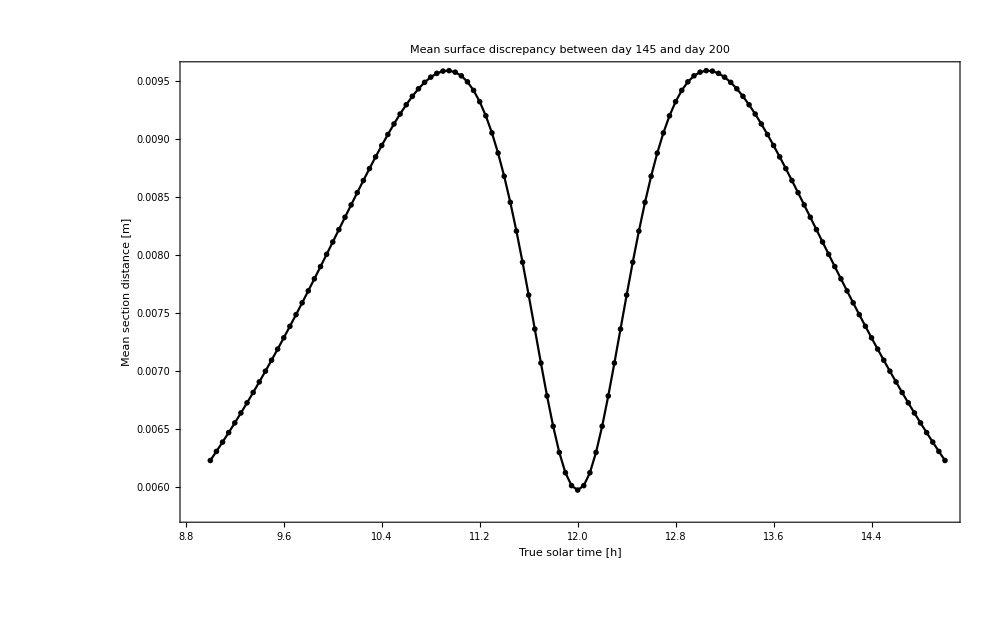

```mathematica
sectionErrors=Table[
(*Mean[...] computes the average of all pointwise distances obtained when comparing section k of both days.*)
Mean[
(*MapThread applies EuclideanDistance by pairing elements from the two lists:
-SurfacesDay145[[k]]->list of points from section k of day 145
-SurfacesDay200[[k]]->list of points from section k of day 200 
If both lists were,for example:
{p1,p2,p3} 
{q1,q2,q3} 
then it would compute:
EuclideanDistance[p1,q1] 
EuclideanDistance[p2,q2] 
EuclideanDistance[p3,q3] 
producing a list of distances.*)
MapThread[EuclideanDistance,{SurfacesDay145[[k]],SurfacesDay200[[k]]}]],
(*The index k runs through all available sections in SurfacesDay145.It is assumed that SurfacesDay200 has the same structure and the same number of corresponding sections.*)
{k,1,Length[SurfacesDay145]}];

(*----------------------------------------------------------------*)
(*Construction of true solar time (TST) values*)
(*----------------------------------------------------------------*)

(*Range[12-3,12+3,0.05] generates times from 9 h to 15 h in steps of 0.05 hours.Since 0.05 h=3 minutes,this list represents a temporal grid with 3-minute resolution around solar noon.That is:9.00,9.05,9.10,...,14.95,15.00 Each of these values will be associated with the mean error computed for the corresponding section.*)

tstValues=Range[12-3,12+3,0.05];

(*----------------------------------------------------------------*)
(*Graphical representation of the mean error versus TST*)
(*----------------------------------------------------------------*)

ListLinePlot[(*ListLinePlot requires pairs {x,y}.Here:
x=tstValues 
y=sectionErrors 
Transpose[{tstValues,sectionErrors}] builds the list:{{t1,e1},{t2,e2},...,{tn,en}} 
where:
ti=true solar time value 
ei=mean error of the corresponding section*)
Transpose[{tstValues,sectionErrors}],
(*Draw a complete frame around the plot*)
Frame->True,
(*Axis labels*)
FrameLabel->{Style["True solar time [h]",20,Black,Bold],Style["Mean section distance [m]",20,Black,Bold]},
(*Figure title*)
PlotLabel->Style["Mean surface discrepancy between day 145 and day 200",24,Black,Bold],
(*Monochrome visual style*)
PlotTheme->"Monochrome",
(*Typographic style of labels and title*)
LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000]
```

```mathematica
(*Extraction of surfaces and focal trajectories*)
(*Mirror surface and focal trajectory for day 170.*)
day170=GenerateSurfaceAndFocus[170];
day176=GenerateSurfaceAndFocus[176];
SurfacesDay170=day170["Surface"];
ReactorDay170=day170["Focus"];

(*Mirror surface and focal trajectory for day 176.*)
SurfacesDay176=day176["Surface"];
ReactorDay176=day176["Focus"];
```

```mathematica
surfacePointDistances=MapThread[EuclideanDistance,{Flatten[SurfacesDay170,1],Flatten[SurfacesDay176,1]}];
focusPointDistances=MapThread[EuclideanDistance,{Flatten[ReactorDay170,1],Flatten[ReactorDay176,1]}];
surfaceMaxError=Max[surfacePointDistances];
surfaceMeanError=Mean[surfacePointDistances];
surfaceRMSError=Sqrt[Mean[surfacePointDistances^2]];
focusMaxError=Max[focusPointDistances];
focusMeanError=Mean[focusPointDistances];
focusRMSError=Sqrt[Mean[focusPointDistances^2]];
comparisonSummary={"Surface max error [m]"->surfaceMaxError,"Surface mean error [m]"->surfaceMeanError,"Surface RMS error [m]"->surfaceRMSError,"Focus max error [m]"->focusMaxError,"Focus mean error [m]"->focusMeanError,"Focus RMS error [m]"->focusRMSError}
```

{Surface max error [m]→0.0000505361,Surface mean error [m]→0.000018596,Surface RMS error [m]→0.0000212276,Focus max error [m]→3.11953×10^-6,Focus mean error [m]→2.25404×10^-6,Focus RMS error [m]→2.29807×10^-6}

```mathematica
relativeComparisonSummary={"Surface max error / FacadeLength"->surfaceMaxError/FacadeLength,"Surface RMS error / FacadeLength"->surfaceRMSError/FacadeLength,"Focus max error / FacadeLength"->focusMaxError/FacadeLength,"Focus RMS error / FacadeLength"->focusRMSError/FacadeLength}
```

{Surface max error / FacadeLength→1.68454×10^-6,Surface RMS error / FacadeLength→7.07587×10^-7,Focus max error / FacadeLength→1.03984×10^-7,Focus RMS error / FacadeLength→7.66023×10^-8}

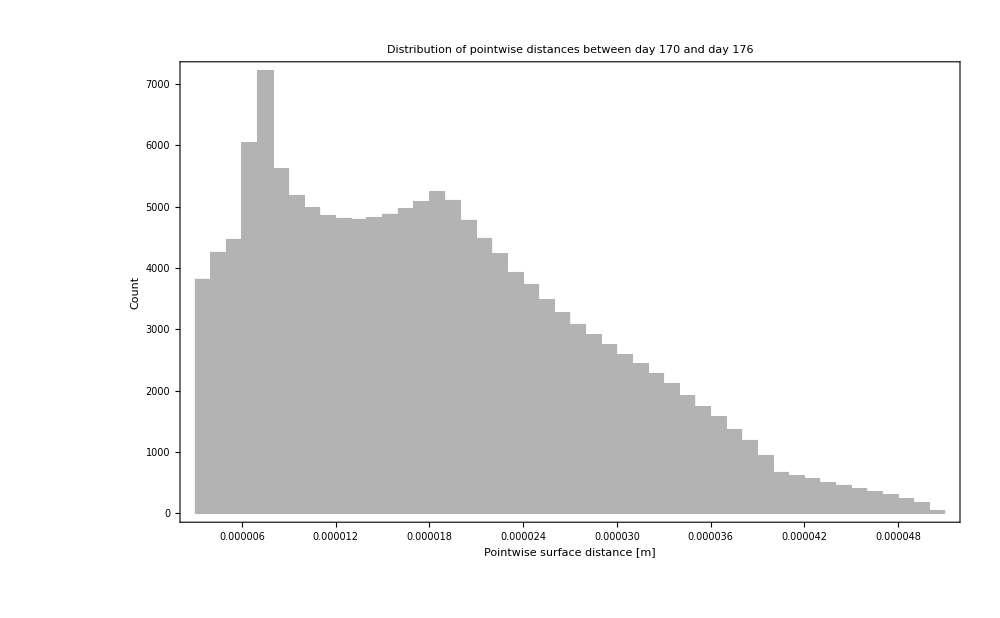

```mathematica
Histogram[surfacePointDistances,40,(*number of bins to resolve the distribution with sufficient detail*)Frame->True,FrameLabel->{Style["Pointwise surface distance [m]",20,Black,Bold],(*horizontal axis:geometric deviation*)Style["Count",20,Black,Bold] 
  (*vertical axis:number of points in each bin*)},PlotLabel->Style["Distribution of pointwise distances between day 170 and day 176",24,Black,Bold],PlotTheme->"Monochrome",(*clean visualization for publication*)LabelStyle->Directive[Black,Bold] (*consistent formatting*),TicksStyle->Directive[Black,18],FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000    ]
```

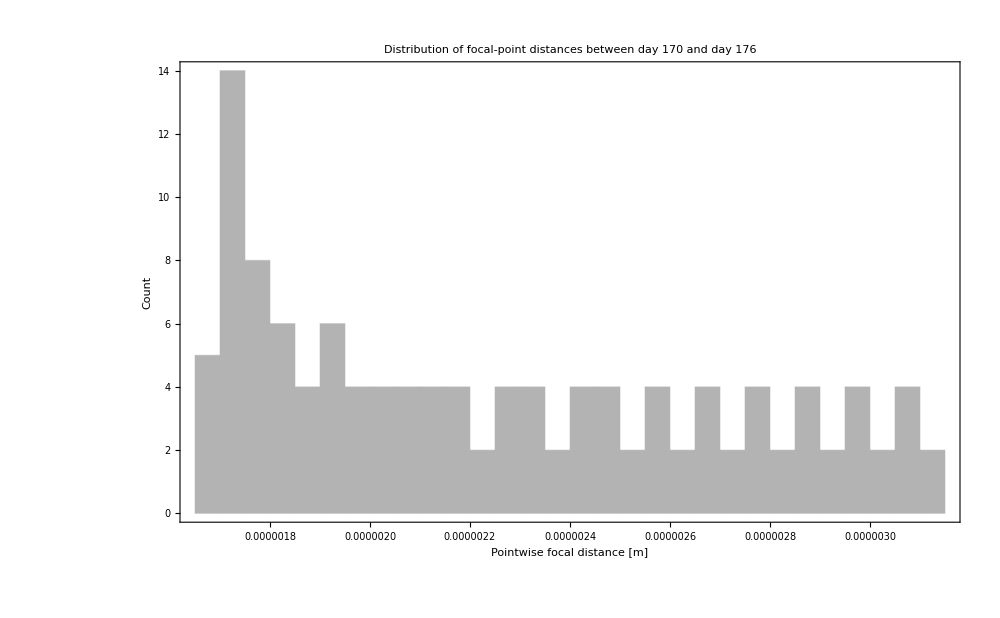

```mathematica
Histogram[focusPointDistances,30,Frame->True,FrameLabel->{Style["Pointwise focal distance [m]",20,Black,Bold],Style["Count",20,Black,Bold]},PlotLabel->Style["Distribution of focal-point distances between day 170 and day 176",24,Black,Bold],PlotTheme->"Monochrome",LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000 ]
```

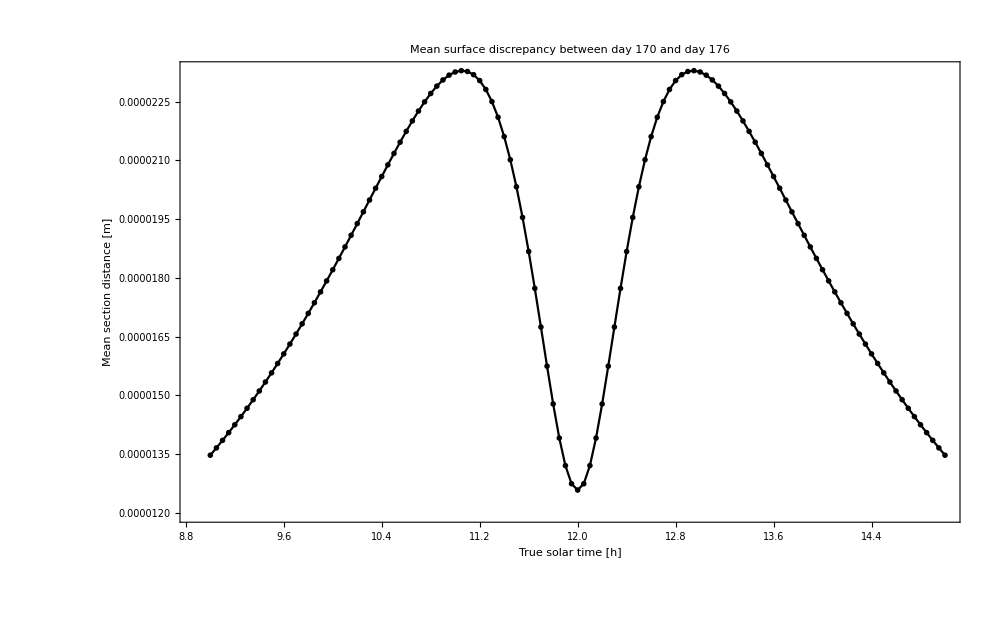

```mathematica
sectionErrors=Table[Mean[MapThread[EuclideanDistance,{SurfacesDay170[[k]],SurfacesDay176[[k]]}]],{k,1,Length[SurfacesDay170]}];
tstValues=Range[12-3,12+3,0.05];
ListLinePlot[Transpose[{tstValues,sectionErrors}],Frame->True,FrameLabel->{Style["True solar time [h]",20,Black,Bold],Style["Mean section distance [m]",20,Black,Bold]},PlotLabel->Style["Mean surface discrepancy between day 170 and day 176",24,Black,Bold],PlotTheme->"Monochrome",LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000 ]
```

The overlap between the surfaces generated for day 170 and day 176 can be inspected visually,but a quantitative comparison is more informative. Since both surfaces are generated using the same parameter sampling in solar time and in the parabola parameter t,a pointwise comparison can be performed directly.This makes it possible to evaluate the maximum,mean,and RMS discrepancy between both mirror surfaces and between their corresponding focal trajectories.If these discrepancies remain small compared with the characteristic dimensions of the system,both days can be considered geometrically equivalent for practical design purposes.

## Validation

#### Animation of the daily evolution of the parabolic profile with a fixed reactor cross-section

This section prepares the elements required to construct an animation in the x–z plane where:
	-The evolution of the parabolic profile throughout the day is shown.
	-A fixed circular section representing the reactor is superimposed.

Physical interpretation:
	A reactor with a fixed circular cross-section (given diameter) is considered,and it is analyzed whether the focal point of the parabola (which moves over time) remains within that section.

The geometric construction of the circle is defined such that:
	-The focal point in the morning (start of operation) coincides with the lower point of the circle.
	-The focal point at solar noon coincides with the upper point of the circle.

Thus,the circle defines the admissible vertical range of the focal-point motion.

```mathematica
(*----------------------------------------------------------------*)
(*Definition of reactor size*)
(*----------------------------------------------------------------*)
(*Reactor diameter (in meters)*)
reactorDiameter=0.65;

(*Reactor radius*)
reactorRadius=reactorDiameter/2;

(*----------------------------------------------------------------*)
(*Definition of key times of the day (True Solar Time)*)
(*----------------------------------------------------------------*)

(*Start of the operating interval (morning)*)
morningTST=9;

(*Solar noon*)
noonTST=12;

(*End of the operating interval (afternoon)*)
afternoonTST=15;

(*----------------------------------------------------------------*)
(*Horizontal position of the reactor*)
(*----------------------------------------------------------------*)

(*The reactor center in x is defined as the midpoint between:
-The focal position in the morning
-The focal position at noon 
fxLocal[t] returns the x-coordinate of the focal point at time t.
This places the reactor "centered" with respect to the horizontal displacement of the focal point during the first half of the day.*)

reactorCenterX=(fxLocal[morningTST]+fxLocal[noonTST])/2;

(*----------------------------------------------------------------*)
(*Vertical position of the reactor*)
(*----------------------------------------------------------------*)

(*The reactor center in z is defined as the midpoint between:
-The focal height in the morning
-The focal height at noon

 fzLocal[t] returns the z-coordinate of the focal point.

This choice ensures that:
-The morning focal point lies at the lower point of the circle.
-The noon focal point lies at the upper point of the circle.

In other words,the circle diameter exactly matches the vertical displacement of the focal point over this interval.*)
reactorCenterZ=(fzLocal[morningTST]+fzLocal[noonTST])/2;

(*----------------------------------------------------------------*)
(*Parametric representation of the reactor circular cross-section*)
(*----------------------------------------------------------------*)

(*A parametric representation of the circle is defined using a parameter s:
-s∈[0,2π]
-Cos[s] and Sin[s] generate the unit circle
-The circle is scaled by the radius and translated to the center (reactorCenterX,reactorCenterZ)
 Result:reactorCircle[s] returns a point {x,z} on the circle.*)

reactorCircle[s_]:={reactorCenterX+reactorRadius Cos[s],(*x-coordinate*)reactorCenterZ+reactorRadius Sin[s]  (*z-coordinate*)};
```

Animation of the daily evolution of the local parabolic profile with the fixed reactor cross-section and the focal trajectory

```mathematica
Animate[
(*For each value of TST,a composite figure is built with Show[...] by superimposing several graphical layers:
1. The local parabolic profile in the x-z plane.
2. The fixed circular cross-section of the reactor.
3. The instantaneous focal-point position at that TST.
4. Three reference points corresponding to morning,noon,and afternoon.*)
Show[
(*------------------------------------------------------------*)
(*1. Local parabolic profile for the current TST*)
(*------------------------------------------------------------*)
ParametricPlot[{xLocal[t,TST],zLocal[t,TST]},(*parameterized curve in the x-z plane*){t,-4,4},(*parameter sweeping the profile*)PlotStyle->Thick,(*draw the curve with a thick line*)Frame->True,(*use a full frame instead of simple axes*)FrameLabel->{Style["x [m]",20,Black,Bold],Style["z [m]",20,Black,Bold]},(*axis labels*)PlotRange->All (*automatically adjust to include the full geometry*),ImageSize->700],

(*------------------------------------------------------------*)
(*2. Fixed circular cross-section of the reactor*)
(*------------------------------------------------------------*)
ParametricPlot[reactorCircle[s],(*parametric representation of the reactor circle*){s,0,2 Pi},(*trace the full circumference*)PlotStyle->{Black,Thick} (*black circle with thick line*)],

(*------------------------------------------------------------*)
(*3. Instantaneous focal-point position for the current TST*)
(*------------------------------------------------------------*)
Graphics[{Red,(*red color to highlight the current focal point*)PointSize[Large],(*large point size*)Point[{fxLocal[TST],fzLocal[TST]}] (*current focal-point coordinates at time TST*)}],

(*------------------------------------------------------------*)
(*4. Reference points at key times of the day*)
(*------------------------------------------------------------*)ListPlot[{{fxLocal[morningTST],fzLocal[morningTST]},(*morning focal point*){fxLocal[noonTST],fzLocal[noonTST]},(*noon focal point*){fxLocal[afternoonTST],fzLocal[afternoonTST]} (*afternoon focal point*)},
(*Different colors are assigned to the three points:
-blue for morning,
-dark green for noon,
-blue for afternoon.*)
PlotStyle->{Blue,Darker[Green],Blue},
(*Markers:
-star for morning,
-triangle for noon,
-star for afternoon.
This helps to visually distinguish the key positions.*)
PlotMarkers->{{"⋆",16},{"△",16},{"⋆",16}}],FrameTicksStyle->Directive[Black,Bold,18]],
(*--------------------------------------------------------------*)
(*Animation parameter:true solar time*)
(*--------------------------------------------------------------*)
{TST,9,15,Appearance->"Labeled"},(*TST varies from 9 to 15 hours.Appearance->"Labeled" adds a labeled slider to display the current time value.*)
AnimationRunning->False
(*The animation does not start automatically.The user decides when to start it or move the slider manually.*)]
```

#### Step 1 : Definition of the fixed section of the reactor and verification of the confinement of the focus path

```mathematica
(*----------------------------------------------------------------*)
(*Basic reactor geometry*)
(*----------------------------------------------------------------*)

(*Reactor diameter,expressed in meters*)
reactorDiameter=0.65; (*m*)

(*Reactor radius:half of the diameter*)
reactorRadius=reactorDiameter/2;
```

Definition of the operating interval

The range of true solar time (TST) over which the focal trajectory is analyzed is defined as:
	-start:9 h
	-end:15 h
	-step:0.01 h 
	
Since 0.01 h=0.6 min=36 s,a relatively fine temporal discretization is used.

```mathematica
tstMin=9;
tstMax=15;
tstStep=0.01;

(*Time grid:list of all TST values within the operating interval*)
tstGrid=Range[tstMin,tstMax,tstStep];
```

Focal trajectory in the local x–z plane for day 170

For each TST value in the time grid,the focal position in the local x–z plane is computed. It is assumed that:
	-fxLocal[TST] gives the x-coordinate of the focus
	-fzLocal[TST] gives the z-coordinate of the focus 

The result focalPath170 is a list of pairs:{{x1,z1},{x2,z2},...,{xn,zn}} describing the full focal trajectory during the day.

```mathematica
focalPath170=Table[{fxLocal[TST],fzLocal[TST]},{TST,tstGrid}];
```

```mathematica
(*----------------------------------------------------------------*)
(*Extreme focal positions in height*)
(*----------------------------------------------------------------*)

(*Extract the second coordinate (z) of all focal points and compute the minimum value.
focalPath170[[All,2]] means:"take the second component of all elements in focalPath170".*)
minFocusZ=Min[focalPath170[[All,2]]];

(*Maximum height reached by the focus during the operating interval*)
maxFocusZ=Max[focalPath170[[All,2]]];

(*----------------------------------------------------------------*)
(*Definition of a simplified fixed reactor cross-section*)
(*----------------------------------------------------------------*)

(*A fixed circular reactor section is defined by its center and radius.Adopted criterion:-Horizontal coordinate of the center:mean of all focal x-positions.This places the reactor approximately centered with respect to the global horizontal displacement of the focus.*)
reactorCenterX=Mean[focalPath170[[All,1]]];

(*Vertical coordinate of the center:midpoint between minimum and maximum focal heights.This centers the circle with respect to the total vertical excursion of the focus.*)
reactorCenterZ=(minFocusZ+maxFocusZ)/2;

(*----------------------------------------------------------------*)
(*Parametric representation of the reactor circular section*)
(*----------------------------------------------------------------*)

(*reactorCircle[s] returns a point {x,z} on the circumference that represents the reactor cross-section.Standard parametrization:x=x_c+R cos(s) z=z_c+R sin(s) with s in[0,2π].*)
reactorCircle[s_]:={reactorCenterX+reactorRadius Cos[s],reactorCenterZ+reactorRadius Sin[s]};

(*----------------------------------------------------------------*)
(*Distance of each focal position to the reactor center*)
(*----------------------------------------------------------------*)

(*For each point in the focal trajectory,compute its distance to the reactor center.-# represents a point {x,z} in focalPath170-{reactorCenterX,reactorCenterZ} is the circle center-Norm[#-center] computes the Euclidean distance- /@applies the function to all points*)
focalDistancesToCenter=Norm[#-{reactorCenterX,reactorCenterZ}]&/@focalPath170;

(*----------------------------------------------------------------*)
(*Maximum focal excursion and remaining safety margin*)
(*----------------------------------------------------------------*)

(*maxFocalExcursion is the maximum distance from the focus to the reactor center over the entire operating interval.Geometrically,it represents the minimum radius required for the reactor to fully contain the focal trajectory.*)
maxFocalExcursion=Max[focalDistancesToCenter];

(*Remaining radial margin:-reactorMargin>0->trajectory fully contained (safety margin)-reactorMargin=0->trajectory touches the boundary-reactorMargin<0->part of the trajectory lies outside*)
reactorMargin=reactorRadius-maxFocalExcursion;

(*----------------------------------------------------------------*)
(*Quantitative summary of the containment analysis*)
(*----------------------------------------------------------------*)

(*A list of rules is constructed to summarize the key quantities.This facilitates quick inspection of whether the proposed reactor geometry fully contains the focal trajectory.*)
containmentSummary={"Reactor radius [m]"->reactorRadius,"Minimum focal height [m]"->minFocusZ,"Maximum focal height [m]"->maxFocusZ,"Vertical focal excursion [m]"->(maxFocusZ-minFocusZ),"Maximum distance from reactor center [m]"->maxFocalExcursion,"Remaining radial margin [m]"->reactorMargin};

(*Display summary*)
containmentSummary
```

{Reactor radius [m]→0.325,Minimum focal height [m]→0.754237,Maximum focal height [m]→0.969758,Vertical focal excursion [m]→0.215522,Maximum distance from reactor center [m]→0.260759,Remaining radial margin [m]→0.0642415}

#### Joint visualization of the reactor cross-section and the daily focal trajectory in the local x–z plane

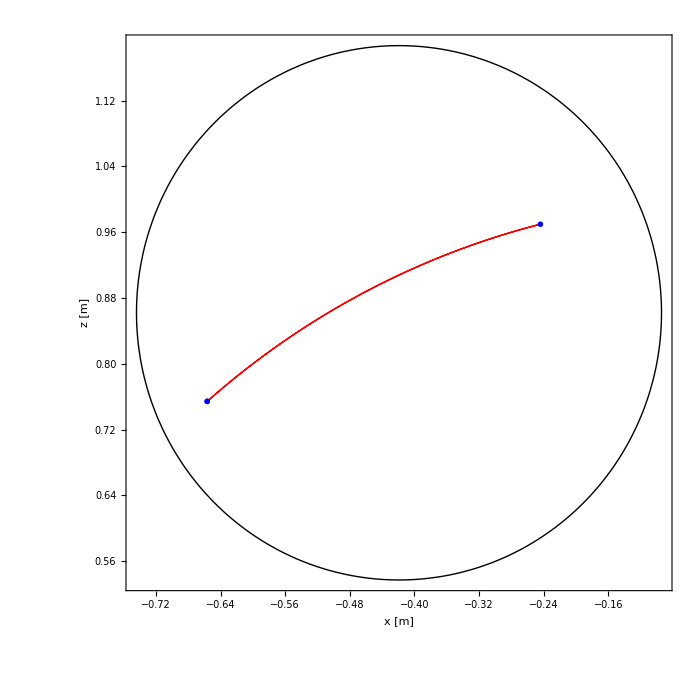

```mathematica
Show[
(*--------------------------------------------------------------*)
(*1. Fixed circular section of the reactor*)
(*--------------------------------------------------------------*)ParametricPlot[reactorCircle[s],(*circle parametrization*){s,0,2 Pi},(*full circle traversal*)PlotStyle->{Black,Thick,Large},(*thick black circle*)Frame->True,(*use full frame*)FrameLabel->{Style["x [m]",24,Black,Bold],Style["z [m]",24,Black,Bold]},(*axis labels*)PlotRange->All,(*include entire visible geometry*)FrameTicksStyle->Directive[Black,Bold,18],ImageSize->700],

(*--------------------------------------------------------------*)
(*2. Full focal trajectory during day 170*)
(*--------------------------------------------------------------*)ListLinePlot[focalPath170,(*list of focal points {x,z}*)PlotStyle->{Red,Thick,Large} (*thick red line*)],

(*--------------------------------------------------------------*)
(*3. Markers at three representative times of the day*)
(*--------------------------------------------------------------*)ListPlot[{First[focalPath170],(*morning:first point*)focalPath170[[Round[Length[focalPath170]/2]]],(*around noon*)Last[focalPath170]                           (*afternoon:last point*)},(*Assigned colors:-blue for morning-dark green for noon-blue for afternoon*)PlotStyle->{Blue,Darker[Green],Blue},(*Markers:-star for morning-triangle for noon-star for afternoon*)PlotMarkers->{{"⋆",14},{"△",14},{"⋆",14}}]]
```

#### Interactive continuous ray tracing on the local parabolic mirror section

This interactive visualization shows,in the local x–z plane:
	-the local parabolic mirror section,
	-the corresponding geometric focus,
	-the parabola vertex,
	-the local optical axis,
	-a bundle of parallel incident rays,
	-and the reflected rays directed toward the focus.

Physical interpretation:
	The incident radiation is modeled as a plane wave,i.e.,as a family of parallel rays arriving from the concave side of the reflector.

The direction of these incident rays is defined by the local optical axis of the parabola,given by the line joining:
	-the geometric focus,
	-and the vertex of the parabolic section.

Then, from each point of incidence on the mirror,a reflected ray is drawn toward the geometric focus,reproducing the ideal optical property of a parabola.

Additionally,a fixed red circle is superimposed,representing the cross-section of the distributed reactor.

```mathematica
(*----------------------------------------------------------------*)
(*Analyzed day*)
(*----------------------------------------------------------------*)
(*Day of the year used in the solar elevation calculation*)
dn=170;

(*----------------------------------------------------------------*)
(*Reactor geometry*)
(*----------------------------------------------------------------*)
(*Reactor diameter (in meters)*)
reactorDiameter=0.65;

(*Reactor radius*)
reactorRadius=reactorDiameter/2;

(*----------------------------------------------------------------*)
(*Daily focal trajectory used to position the reactor*)
(*----------------------------------------------------------------*)
(*A TST grid from 9 h to 15 h with step 0.01 h is constructed.This grid is used to estimate the daily focal trajectory.*)
tstGrid=Range[9,15,0.01];

(*Focal trajectory for day 170 in the local x–z plane.Each element is a point {x,z}.*)

focalPath170=Table[{fxLocal[TST],fzLocal[TST]},{TST,tstGrid}];

(*Horizontal center of the reactor:mean of focal x-positions*)
reactorCenterX=Mean[focalPath170[[All,1]]];

(*Vertical center:midpoint between minimum and maximum focal height*)
reactorCenterZ=(Min[focalPath170[[All,2]]]+Max[focalPath170[[All,2]]])/2;

(*Parametric representation of the reactor circular cross-section*)
reactorCircle[s_]:={reactorCenterX+reactorRadius Cos[s],reactorCenterZ+reactorRadius Sin[s]};

(*----------------------------------------------------------------*)
(*Local geometric definitions of the parabolic mirror*)
(*----------------------------------------------------------------*)
(*Mirror point in the local surface for parameter t and time TST*)
mirrorPoint[t_,TST_]:={xLocal[t,TST],zLocal[t,TST]};

(*Geometric focal point*)
focusPoint[TST_]:={fxLocal[TST],fzLocal[TST]};

(*Parabola vertex (taken at t=0)*)
vertexPoint[TST_]:=mirrorPoint[0,TST];

(*----------------------------------------------------------------*)
(*Local optical axis*)
(*----------------------------------------------------------------*)
(*Direction defined by the vector from focus to vertex,normalized*)
axisDirection[TST_]:=Normalize[vertexPoint[TST]-focusPoint[TST]];

(*----------------------------------------------------------------*)
(*Incident ray segments*)
(*----------------------------------------------------------------*)
(*Generates an incident ray segment at a given mirror point*)
incidentSegment[t_,TST_,len_]:=Module[{p,s},p=mirrorPoint[t,TST];
s=axisDirection[TST];
Line[{p-len s,p}]];

(*----------------------------------------------------------------*)
(*Reflected ray segments*)
(*----------------------------------------------------------------*)

(*Generates a reflected ray segment directed toward the focus*)
reflectedSegment[t_,TST_,len_]:=Module[{p,f,dir},p=mirrorPoint[t,TST];
f=focusPoint[TST];
dir=Normalize[f-p];
Line[{p,p+len dir}]];

(*----------------------------------------------------------------*)
(*Interactive interface*)
(*----------------------------------------------------------------*)
Manipulate[Module[{tVals,mirrorCurve,reactorPlot,incidentRays,reflectedRays,focusPlot,vertexPlot,axisPlot,focus,vertex,titleText,solarText},(*Sampling points on the mirror*)tVals=Subdivide[-tMax,tMax,nrays-1];
focus=focusPoint[TST];
vertex=vertexPoint[TST];
titleText=Row[{"Ray tracing at TST = ",NumberForm[TST,{3,2}]," h"}];
solarText=Row[{"Solar elevation h = ",NumberForm[h[dn,TST]*180/Pi,{4,2}],"°"}];
(*Mirror curve*)mirrorCurve=ParametricPlot[{xLocal[t,TST],zLocal[t,TST]},{t,-tMax,tMax},PlotStyle->{Black,Thick}];
(*Reactor*)reactorPlot=ParametricPlot[reactorCircle[s],{s,0,2 Pi},PlotStyle->{Red,Thick}];
(*Incident rays*)incidentRays=Graphics[{Directive[Darker[Green],Thick],Table[incidentSegment[t,TST,incidentLength],{t,tVals}]}];
(*Reflected rays*)reflectedRays=Graphics[{Directive[Blue,Thin],Table[reflectedSegment[t,TST,reflectedLength],{t,tVals}]}];
(*Focus and vertex*)focusPlot=Graphics[{Red,PointSize[Large],Point[focus]}];
vertexPlot=Graphics[{Black,PointSize[Medium],Point[vertex]}];
(*Optical axis*)axisPlot=Graphics[{Directive[Gray,Dashed,Thin],Line[{focus-2 axisDirection[TST],vertex+2 axisDirection[TST]}]}];
(*Final composition*)Show[{mirrorCurve,reactorPlot,incidentRays,reflectedRays,focusPlot,vertexPlot,axisPlot},Frame->True,FrameLabel->{Style["x [m]",24,Bold,Black],Style["z [m]",24,Bold,Black]},PlotLabel->Style[Column[{titleText,solarText},Center],20,Bold],PlotRange->{{-7,4},{-1.2,6}},FrameTicksStyle->Directive[Black,Bold,18],ImageSize->1000]],(*Controls*){{TST,12,"true solar time [h]"},9,15,0.05,Appearance->"Labeled"},{{nrays,15,"number of rays"},3,31,1,Appearance->"Labeled"},{{tMax,4,"mirror half-width parameter"},1,6,0.1,Appearance->"Labeled"},{{incidentLength,3.5,"incident-ray length"},0.5,8,0.1,Appearance->"Labeled"},{{reflectedLength,3.0,"reflected-ray length"},0.5,8,0.1,Appearance->"Labeled"},TrackedSymbols:>{TST,nrays,tMax,incidentLength,reflectedLength}]
```

#### Continuous 3 D ray tracing on the parametric mirror surface

This block builds an interactive 3D ray-tracing visualization on the mirror surface for day 170. 

Geometric convention:
	-z is the vertical coordinate.
	-The mirror opens toward the region x<0.
	-Therefore,incident solar radiation must arrive from x<0 toward the concave reflective surface.

Optical convention:
	-All incident rays form a plane wave.
	-Therefore,all incident rays are parallel.
	-For each TST, they share the same elevation and azimuth.
	-Only illuminated points on the concave surface are considered.
	-Reflected directions are computed using the law of reflection.
	-Only reflected rays intersecting the cylindrical reactor are retained.

Requirements:
	-GenerateSurfaceAndFocus[dn] already defined.
	-day170=GenerateSurfaceAndFocus[170] already computed.
	-SurfacesDay170 and ReactorDay170 available.
	-h[dn,TST] and azimuth[dn,TST] defined.*)

```mathematica
(*----------------------------------------------------------------*)
(*INPUT DATA*)
(*----------------------------------------------------------------*)
(*Day of the year*)
dn=170;

(*Discretized mirror surface:grid of 3D points*)
surfaceGrid=SurfacesDay170;

(*Reactor centerline (flattened to a list of 3D points)*)
reactorCenterline=Flatten[ReactorDay170,1];

(*Number of curves and points*)
nCurves=Length[surfaceGrid];
nPts=Length[surfaceGrid[[1]]];

(*----------------------------------------------------------------*)
(*Reactor geometry*)
(*----------------------------------------------------------------*)
(*Reactor radius (65 cm diameter)*)
reactorRadius=0.65/2;

(*Cylindrical representation of the reactor*)
reactorTube=Tube[reactorCenterline,reactorRadius];

(*----------------------------------------------------------------*)
(*AUXILIARY GEOMETRY*)
(*----------------------------------------------------------------*)
(*Local focus for each curve*)
focusOfCurve[i_]:=First[ReactorDay170[[i]]];

(*Approximate surface normal from neighboring points*)
normalAt[i_,j_]:=Module[{i1,i2,j1,j2,tu,tv,n,p,f},i1=Max[1,i-1];
i2=Min[nCurves,i+1];
j1=Max[1,j-1];
j2=Min[nPts,j+1];
(*Tangent directions*)tu=surfaceGrid[[i,j2]]-surfaceGrid[[i,j1]];
tv=surfaceGrid[[i2,j]]-surfaceGrid[[i1,j]];
(*Normal via cross product*)n=Cross[tv,tu];
If[Norm[n]==0,Return[{0,0,1}]];
n=Normalize[n];
(*Orient toward concave side*)p=surfaceGrid[[i,j]];
f=focusOfCurve[i];
If[Dot[n,f-p]<0,n=-n];
n];
```

#### SOLAR DIRECTION

```mathematica
(*Incident solar direction in global XYZ*)
incidentDirection3D[dn_,TST_]:=Normalize[{Cos[h[dn,TST]] Cos[azimuth[dn,TST]],-Cos[h[dn,TST]] Sin[azimuth[dn,TST]],-Sin[h[dn,TST]]}];

(*----------------------------------------------------------------*)
(*ILLUMINATION AND REFLECTION*)
(*----------------------------------------------------------------*)
(*Check if point is illuminated*)
illuminatedQ[i_,j_,TST_]:=Module[{s=incidentDirection3D[dn,TST],n=normalAt[i,j]},Dot[s,n]<0];

(*Reflected direction*)
reflectedDirAt[i_,j_,TST_]:=Module[{s=incidentDirection3D[dn,TST],n=normalAt[i,j]},Normalize[s-2 (s.n) n]];

(*----------------------------------------------------------------*)
(*APPROXIMATE INTERSECTION WITH REACTOR*)
(*----------------------------------------------------------------*)
nearestReactorPoint=Nearest[reactorCenterline->"Index"];

(*Ray-cylinder intersection (approximate)*)
rayHitsTubeQ[p_,r_,rayLen_,nsamp_:60]:=Module[{pts,dmin},pts=Table[p+u rayLen r,{u,0,1,1./nsamp}];
dmin=Min[Table[Norm[q-reactorCenterline[[First@nearestReactorPoint[q]]]],{q,pts}]];
dmin≤reactorRadius];

(*----------------------------------------------------------------*)
(*VIEW CONTROL*)
(*----------------------------------------------------------------*)
viewChoice["3D"]:={2.2,-2.4,1.4};
viewChoice["Top"]:={0,0,10};
viewChoice["SideXZ"]:={0,-10,0};
viewChoice["SideYZ"]:={10,0,0};

(*----------------------------------------------------------------*)
(*MAIN MANIPULATE*)
(*----------------------------------------------------------------*)
Manipulate[Module[{sdir,sampledIndices,incidentLen=1.8,reflectedLen=2.4,incidentRays={},reflectedRays={},elevDeg,azDeg,titleText,centralPoint,solarArrow},(*Solar direction*)sdir=incidentDirection3D[dn,TST];
elevDeg=h[dn,TST]*180/Pi;
azDeg=azimuth[dn,TST]*180/Pi;
(*Sparse sampling for performance*)sampledIndices=Flatten[Table[{i,j},{i,1,nCurves,curveStep},{j,1,nPts,pointStep}],1];
(*Ray construction*)Do[Module[{i=idx[[1]],j=idx[[2]],p,r},p=surfaceGrid[[i,j]];
If[illuminatedQ[i,j,TST],AppendTo[incidentRays,Line[{p-incidentLen sdir,p}]];
r=reflectedDirAt[i,j,TST];
If[rayHitsTubeQ[p,r,reflectedLen],AppendTo[reflectedRays,Line[{p,p+reflectedLen r}]]];];],{idx,sampledIndices}];
(*Title*)titleText=Column[{Row[{"3D ray tracing at TST = ",NumberForm[TST,{3,2}]," h"}],Row[{"Solar elevation = ",NumberForm[elevDeg,{4,2}],"°,   ","Solar azimuth = ",NumberForm[azDeg,{5,2}],"°"}]},Center];
(*Final visualization*)Show[{
ListPointPlot3D[Flatten[surfaceGrid,1],PlotStyle->{Black,PointSize[0.0025]},BoxRatios->{1,1,0.6}],
Graphics3D[{Red,Opacity[0.28],reactorTube}],
Graphics3D[{Red,PointSize[0.01],Point[reactorCenterline]}],
Graphics3D[{Darker[Green],Thick,incidentRays}],
Graphics3D[{Blue,Thick,reflectedRays}]
},Axes->True,AxesLabel->{Style["x [m]",24,Bold],Style["y [m]",24,Bold],Style["z [m]",24,Bold]},PlotLabel->Style[titleText,24,Bold],ViewPoint->viewChoice[viewMode],ViewProjection->"Orthographic",ImageSize->1000
]
],(*Controls*){{TST,9,"true solar time [h]"},9,15,0.05,Appearance->"Labeled"},{{curveStep,14,"curve step"},6,24,1,Appearance->"Labeled"},{{pointStep,120,"point step"},40,180,10,Appearance->"Labeled"},{{viewMode,"3D","view"},{"3D","Top","SideXZ","SideYZ"}},TrackedSymbols:>{TST,curveStep,pointStep,viewMode}]
```

#### Continuous power - density distribution on the reactor skin

This block computes and visualizes the power-density distribution over the lateral surface of the reactor,unwrapped into 2D.

Final map coordinates:
	-Horizontal axis:position along the reactor[m],from 0 to approximately 30 m.
	-Vertical axis:perimeter coordinate on the reactor skin[m],from 0 to 2 Pi R.

Represented quantity:
	-Power density on the reactor skin[W/m^2].

Important visual remark:
	The upper color limit is fixed using a percentile in order to avoid color saturation and better reveal local variations.*)

ASSUMED AVAILABLE FROM PREVIOUS BLOCKS

This block assumes that the following quantities are already defined or computed:
	-dn
	-surfaceGrid=SurfacesDay170
	-reactorCenterline=Flatten[ReactorDay170,1]
	-nCurves,nPts
	-reactorRadius
	-nearestReactorPoint
	-normalAt[i,j]
	-illuminatedQ[i,j,TST]
	-reflectedDirAt[i,j,TST]
	-h[dn,TST],azimuth[dn,TST] 

If needed,the following lines could be uncommented and adapted:
	dn=170;
	surfaceGrid=SurfacesDay170;
	reactorCenterline=Flatten[ReactorDay170,1];
	nCurves=Length[surfaceGrid];
	nPts=Length[surfaceGrid[[1]]];
	reactorRadius=0.65/2;
	nearestReactorPoint=Nearest[reactorCenterline→"Index"];*)

```mathematica
(*----------------------------------------------------------------*)
(*CORRECTED INCIDENT DIRECTION*)
(*----------------------------------------------------------------*)
(*Propagation direction of the incident solar beam in the global XYZ system.

Components:
-horizontal projection controlled by azimuth,
-vertical component controlled by solar elevation h.

The negative sign in the vertical component indicates that the beam travels downward from the Sun toward the mirror.*)incidentDirection3D[dn_,TST_]:=Normalize[{Cos[h[dn,TST]] Cos[azimuth[dn,TST]],-Cos[h[dn,TST]] Sin[azimuth[dn,TST]],-Sin[h[dn,TST]]}];

(*----------------------------------------------------------------*)
(*USER PARAMETERS*)
(*----------------------------------------------------------------*)
(*Effective mirror reflectivity.This factor reduces the incident power in order to obtain the actually reflected power.*)
rhoMirror=0.60;

(*Simplified DNI (Direct Normal Irradiance) model. If a real measured or more detailed model is available,this function should be replaced accordingly.Here,a Gaussian law centered at TST=12 h is used,with a maximum value close to 900 W/m^2.*)
dniFunction[TST_]:=900 Exp[-0.08 (TST-12)^2];

(*Length used to trace reflected rays*)
rayTraceLength=3.0;

(*Smoothing widths for the final map:
-sigmaS controls smoothing along the reactor axis,
-sigmaU controls smoothing along the reactor perimeter,both in meters.*)
sigmaS=2.5;(*meters along the reactor*)
sigmaU=0.08;(*meters along the perimeter*)

(*----------------------------------------------------------------*)
(*BASIC REACTOR GEOMETRY*)
(*----------------------------------------------------------------*)
(*Number of points discretizing the reactor centerline*)
nS=Length[reactorCenterline];

(*Total perimeter length of the circular reactor cross-section*)
perimeterLength=2 Pi reactorRadius;

(*Local length of each centerline segment.For each point k:
-if it is not the last point,the distance to the next point is used,
-if it is the last point,the distance to the previous point is used.*)
segmentLengths=Table[If[k<nS,Norm[reactorCenterline[[k+1]]-reactorCenterline[[k]]],Norm[reactorCenterline[[k]]-reactorCenterline[[k-1]]]],{k,1,nS}];

(*Accumulated axial coordinate s along the reactor.sCoordinate[[k]] represents the longitudinal position of point k on the reactor centerline.*)
sCoordinate=Accumulate[Prepend[Most[segmentLengths],0]];

(*Approximate total reactor length*)
reactorLength=Last[sCoordinate]+Last[segmentLengths];

(*----------------------------------------------------------------*)
(*LOCAL MIRROR PATCH AREA*)
(*----------------------------------------------------------------*)
(*patchAreaAt[i,j] estimates the local area of the small mirror patch associated with surface-grid point (i,j). 
Method:
-approximate tangential vectors are taken in the two grid directions,
-the norm of their cross product gives the parallelogram area,
-division by 4 compensates for the use of centered differences.*)
patchAreaAt[i_,j_]:=Module[{i1,i2,j1,j2,tu,tv},i1=Max[1,i-1];
i2=Min[nCurves,i+1];
j1=Max[1,j-1];
j2=Min[nPts,j+1];
tu=surfaceGrid[[i,j2]]-surfaceGrid[[i,j1]];
tv=surfaceGrid[[i2,j]]-surfaceGrid[[i1,j]];
Norm[Cross[tv,tu]]/4];

(*----------------------------------------------------------------*)
(*FIRST INTERSECTION OF REFLECTED RAY WITH REACTOR*)
(*----------------------------------------------------------------*)
(*firstTubeHit[p,r,rayLen] searches approximately for the first intersection point between a reflected ray and the reactor tube.
Parameters:
-p:ray origin on the mirror,
-r:unit reflected direction,
-rayLen:maximum tracing length,
-nsamp:number of sampling points along the segment.

Method:
-the ray segment is discretized,
-for each sample, its distance to the reactor axis is computed,
-the first sample entering within the reactor radius is detected.*)
firstTubeHit[p_,r_,rayLen_,nsamp_:200]:=Module[{pts,dists,idx},pts=Table[p+u rayLen r,{u,0,1,1./nsamp}];
dists=Table[Norm[q-reactorCenterline[[First@nearestReactorPoint[q]]]],{q,pts}];
idx=FirstPosition[dists,_?(#≤reactorRadius&),Missing["NotFound"]];
If[idx===Missing["NotFound"],Nothing,pts[[idx[[1]]]]]];

(*----------------------------------------------------------------*)
(*LOCAL FRAME ON THE REACTOR*)
(*----------------------------------------------------------------*)
(*reactorTangentAt[k] estimates the unit tangent vector of the reactor centerline at point k.*)
reactorTangentAt[k_]:=Module[{k1,k2,t},k1=Max[1,k-1];
k2=Min[nS,k+1];
t=reactorCenterline[[k2]]-reactorCenterline[[k1]];
Normalize[t]];

(*reactorFrameAt[k] constructs a local orthonormal basis on the reactor at point k:
-e1,e2:orthogonal directions in the plane normal to the axis,-t:tangent to the reactor axis. This basis is used to convert a 3D impact point into axial and perimeter coordinates.*)
reactorFrameAt[k_]:=Module[{t,ref,e1,e2},t=reactorTangentAt[k];
ref={0,0,1};(*auxiliary reference vector*)If[Abs[t.ref]>0.9,ref={1,0,0}];
e1=Normalize[ref-(ref.t) t];
e2=Normalize[Cross[t,e1]];
{e1,e2,t}];

(*----------------------------------------------------------------*)
(*MAP A HIT POINT TO UNWRAPPED COORDINATES*)
(*----------------------------------------------------------------*)
(*hitCoordinatesOnTube[q] maps a 3D impact point q on the reactor tube to unwrapped coordinates:-s:axial coordinate along the reactor,-u:perimeter coordinate on the reactor skin,-k:index of the nearest centerline point. This allows conversion from 3D geometry to a 2D unwrapped map of the cylindrical surface.*)
hitCoordinatesOnTube[q_]:=Module[{k,c,e1,e2,t,radial,theta,u,s},k=First@nearestReactorPoint[q];
c=reactorCenterline[[k]];
{e1,e2,t}=reactorFrameAt[k];
radial=q-c;
If[Norm[radial]==0,radial=e1];
radial=Normalize[radial];
theta=Mod[ArcTan[radial.e1,radial.e2],2 Pi];
u=reactorRadius theta;
s=sCoordinate[[k]];
{s,u,k}];

(*----------------------------------------------------------------*)
(*PERIODIC DISTANCE ALONG THE PERIMETER*)
(*----------------------------------------------------------------*)
(*Minimum distance between two positions u1 and u2 on a circular perimeter. The minimum is taken between:-the direct difference,-and the wrapped-around periodic distance.*)

periodicPerimeterDifference[u1_,u2_]:=Module[{d},d=Abs[u1-u2];
Min[d,perimeterLength-d]];

(*----------------------------------------------------------------*)
(*WEIGHTED IMPACT CLOUD*)
(*----------------------------------------------------------------*)
(*reactorImpactCloud[TST] builds a cloud of energetic impacts on the reactor skin for a given instant TST. 

For each sampled mirror point:
-illumination is checked,
-the local patch area is estimated,
-reflected power from that patch is computed,
-the reflected ray is traced,
-if it hits the reactor,its unwrapped position and associated power are stored.*)
reactorImpactCloud[TST_,curveStep_:14,pointStep_:120]:=Module[{sdir,sampledIndices,impacts={},p,n,dA,localPower,r,hit,coords,sval,uval,k},sdir=incidentDirection3D[dn,TST];
sampledIndices=Flatten[Table[{i,j},{i,1,nCurves,curveStep},{j,1,nPts,pointStep}],1];
Do[Module[{i=idx[[1]],j=idx[[2]]},If[illuminatedQ[i,j,TST],p=surfaceGrid[[i,j]];
n=normalAt[i,j];
dA=patchAreaAt[i,j];
(*Reflected power associated with the patch:reflectivity×DNI×cosine factor×area*)localPower=rhoMirror*dniFunction[TST]*Max[0,-incidentDirection3D[dn,TST].n]*dA;
r=reflectedDirAt[i,j,TST];
hit=firstTubeHit[p,r,rayTraceLength];
If[hit=!=Nothing,coords=hitCoordinatesOnTube[hit];
sval=coords[[1]];
uval=coords[[2]];
k=coords[[3]];
AppendTo[impacts,<|"s"->sval,"u"->uval,"k"->k,"Power"->localPower|>];];];],{idx,sampledIndices}];
impacts];

(*----------------------------------------------------------------*)
(*CONTINUOUS POWER-DENSITY FIELD*)
(*----------------------------------------------------------------*)
(*reactorPowerDensityField[TST] transforms the discrete impact cloud into a continuous power-density field over the reactor skin. 
Method:
-a regular grid in (s,u) coordinates is built,
-each impact contributes to nearby nodes through a Gaussian weight,
-division by the cell area yields W/m^2.*)
reactorPowerDensityField[TST_,curveStep_:14,pointStep_:120,nSGrid_:120,nUGrid_:90]:=Module[{impacts,sGrid,uGrid,density,cellArea,sval,uval,num,ds,du},impacts=reactorImpactCloud[TST,curveStep,pointStep];
sGrid=Subdivide[0,reactorLength,nSGrid-1];
uGrid=Subdivide[0,perimeterLength,nUGrid-1];
ds=sGrid[[2]]-sGrid[[1]];
du=uGrid[[2]]-uGrid[[1]];
(*density[[iu,is]] contains the power density in the cell corresponding to position (s,u).*)
density=Table[sval=sGrid[[is]];
uval=uGrid[[iu]];
(*Weighted sum of all impact contributions*)num=Total[Table[impacts[[m,"Power"]]*Exp[-(sval-impacts[[m,"s"]])^2/(2 sigmaS^2)]*Exp[-periodicPerimeterDifference[uval,impacts[[m,"u"]]]^2/(2 sigmaU^2)],{m,1,Length[impacts]}]];
cellArea=ds du;
If[cellArea==0,0,num/cellArea],{iu,1,nUGrid},{is,1,nSGrid}];
<|"Density"->density,"sGrid"->sGrid,"uGrid"->uGrid,"Impacts"->impacts|>];

(*----------------------------------------------------------------*)
(*EXPLICIT DISCRETE FUNCTION*)
(*----------------------------------------------------------------*)
(*powerDensityFunction[TST] returns a discrete function of two indices (iu,is), allowing direct access to the computed density matrix.*)
powerDensityFunction[TST_,curveStep_:14,pointStep_:120,nSGrid_:120,nUGrid_:90]:=Module[{field,density},field=reactorPowerDensityField[TST,curveStep,pointStep,nSGrid,nUGrid];
density=field["Density"];
Function[{iu,is},density[[iu,is]]]];

(*----------------------------------------------------------------*)
(*OPTIONAL LOG-VISUALIZATION VERSION*)
(*----------------------------------------------------------------*)
(*powerMap2DLog[TST] constructs a 2D visualization of the power-density map on the reactor skin. 
Features:
-uses the computed density matrix,
-limits the visual maximum using a percentile,
-applies a logarithmic scale Log[1+x] to highlight variations,-represents the unwrapped reactor with physical axes:s->axial position[m] u->perimeter coordinate[m]*)
powerMap2DLog[TST_,curveStep_:14,pointStep_:120,nSGrid_:120,nUGrid_:90,qPercentile_:0.95]:=Module[{field,density,flat,qmaxVis,qminVis=0,densityVis,cf,sTicksPhysical,uTicksPhysical,xTicks,yTicks},field=reactorPowerDensityField[TST,curveStep,pointStep,nSGrid,nUGrid];
density=field["Density"];
flat=Flatten[density];
qmaxVis=Quantile[flat,qPercentile];
If[qmaxVis≤0,qmaxVis=Max[flat]];
If[qmaxVis≤0,qmaxVis=1];
(*Upper clipping to avoid color saturation*)
densityVis=Map[Min[#,qmaxVis]&,density,{2}];
(*Visual logarithmic scale*)
densityVis=Log[1+densityVis];
(*Color palette*)
cf=ColorData["Rainbow"];
(*Desired physical ticks along the axial direction*)
sTicksPhysical={0,7.5,15,22.5,30};
(*Desired physical ticks along the perimeter*)
uTicksPhysical=N[{0,perimeterLength/4,perimeterLength/2,3 perimeterLength/4,perimeterLength}];
(*Conversion from physical coordinates to ArrayPlot indices*)
xTicks=Table[{1+(nSGrid-1) s/30,NumberForm[s,{4,1}]},{s,sTicksPhysical}];
yTicks=Table[{1+(nUGrid-1) u/perimeterLength,NumberForm[u,{4,2}]},{u,uTicksPhysical}];
ArrayPlot[densityVis,Frame->True,FrameTicks->{{yTicks,None},{xTicks,None}},FrameLabel->{Style["Perimeter coordinate on reactor skin [m]",20,Bold],Style["Position along reactor [m]",20,Bold]},PlotLabel->Style[Row[{"Log-scaled power-density map on reactor skin at TST = ",NumberForm[TST,{3,2}]," h"}],24,Bold],ColorFunction->cf,ColorFunctionScaling->True,PlotRange->All,PlotLegends->BarLegend[{cf,{Log[1+qminVis],Log[1+qmaxVis]}},Ticks->Table[{Log[1+q],NumberForm[q,{6,1}]},{q,Subdivide[0,qmaxVis,5]}],LegendLabel->Style["Power density on skin [W/m^2]",18,Bold],LabelStyle->Directive[Black,18]],FrameTicksStyle->Directive[Black,Bold,19],ImageSize->1000]];
```

```mathematica
powerMap2DLog[9,4,2]
```

-Graphics-

```mathematica
powerMap2DLog[12,4,2]
```

-Graphics-

```mathematica
powerMap2DLog[15,4,2]
```

-Graphics-

## Thermal model on the reactor skin using finite-differences

#### This block computes the steady - state temperature field on the reactor skin from the optical power - density distribution q (s, u) .

Physical effects included :
 	-thermal conduction along the steel wall,
	-convection with ambient air, -thermal radiation to the surroundings .
   
   Coordinates used :
           -s : longitudinal coordinate along the reactor[m]
           -u : perimeter coordinate on the reactor skin[m] 
 
 Boundary conditions :
	-periodic in u (because the reactor is cylindrical),
	-zero flux at s = 0 and s = L (homogeneous Neumann condition) .
      
Solved equation :
rho cp e dT/dt = k_e Laplacian (T) + q - h (T - Tamb) - eps sigma (T^4 - Tamb^4) 

 where :
  	-rho cp e dT/dt represents the surface thermal inertia,
	 -k_e Laplacian (T) represents thermal diffusion in the wall,
	 -q is the incident heat flux,
	 -h (T - Tamb) are convective losses,
	 -eps sigma (T^4 - Tamb^4) are radiative losses .
   
   Numerical strategy :
             The stationary problem is not solved directly; instead, the system is integrated in pseudo - time until convergence is reached . At steady state, dT/dt -> 0.*)

```mathematica
(*----------------------------------------------------------------*)
(*TIMES OF INTEREST*)
(*----------------------------------------------------------------*)

(*Solar times at which the thermal model is evaluated:
-9 h:morning
-12 h:noon
-15 h:afternoon*)
timesToEvaluate={9,12,15};

(*----------------------------------------------------------------*)
(*MATERIAL AND ENVIRONMENT PARAMETERS*)
(*----------------------------------------------------------------*)

(*Ambient temperature in Kelvin.A summer condition of 30 °C is assumed.*)
Tamb=30+273.15;

(*Steel surface emissivity*)
epsSteel=0.80;

(*Stefan-Boltzmann constant[W/m^2/K^4]*)
sigmaSB=5.670374419*10^-8;

(*External convective heat-transfer coefficient[W/m^2/K]*)
hExt=10.0;

(*Steel thermal conductivity[W/m/K]*)
kSteel=16.0;

(*Steel density[kg/m^3]*)
rhoSteelMass=7850.0;

(*Steel specific heat capacity[J/kg/K]*)
cpSteel=500.0;

(*Reactor wall thickness[m]*)
steelThickness=0.003;

(*Air thermal conductivity[W/m/K]*)
kAir=0.026;

(*Steel thermal diffusivity[m^2/s]:alpha=k/(rho cp)*)
alphaSteel=kSteel/(rhoSteelMass cpSteel);

(*----------------------------------------------------------------*)
(*OPTIONAL DIRECT SOLAR INCIDENCE ON THE REACTOR*)
(*----------------------------------------------------------------*)

(*Direct flux field on the reactor.In this version it is taken as zero over the whole surface.

That is,only heating due to mirror-reflected radiation is considered,not direct solar radiation on the tube.

dims is the mesh dimension {nU,nS}.*)
directFluxField[TST_,dims_]:=ConstantArray[0.0,dims];
```

FLUX FIELD ON THE REACTOR SKIN
reactorFluxField builds the total heat-flux field on the reactor skin for a given solar time TST.

Components:
	-qReflected:flux from reflected rays
	-qDirect:direct solar flux on the reactor
	-qTotal:sum of both contributions

```mathematica
reactorFluxField[TST_,curveStep_:4,pointStep_:2,nSGrid_:120,nUGrid_:90]:=Module[{field,qReflected,qDirect,qTotal},
(*field comes from the previous optical block and contains the continuous power-density map on the reactor skin.*)
field=reactorPowerDensityField[TST,curveStep,pointStep,nSGrid,nUGrid];
(*Reflected flux*)
qReflected=field["Density"];
(*Direct flux,taken as zero here*)
qDirect=directFluxField[TST,Dimensions[qReflected]];
(*Total flux*)
qTotal=qReflected+qDirect;
<|"Flux"->qTotal,"sGrid"->field["sGrid"],"uGrid"->field["uGrid"]|>];
```

DISCRETE LAPLACIAN

Array-index convention for T:
	-first index→u (perimeter coordinate)
	-second index→s (longitudinal coordinate) 

Boundary conditions:
	-periodic in u
	-homogeneous Neumann in s (zero flux),implemented with mirror values at the ends.

This operator returns a finite-difference approximation of the 2D Laplacian of T.

```mathematica
discreteLaplacian[T_,ds_,du_]:=Module[{nU,nS,lap,iuP,iuM,isP,isM,Tup,Tdown,Tright,Tleft},

(*Mesh dimensions*)
{nU,nS}=Dimensions[T];

(*Initialize Laplacian matrix*)
lap=ConstantArray[0.0,{nU,nS}];

Do[
(*Neighbor indices in the perimeter direction u.Since the condition is periodic:
-if we are at the last node,the next is the first,
-if we are at the first node,the previous is the last.*)
iuP=If[iu==nU,1,iu+1];
iuM=If[iu==1,nU,iu-1];

(*Neighbor indices in the longitudinal direction s.
Zero flux at the boundaries is implemented using mirror values:
-at the right end use nS-1,
-at the left end use 2.*)
isP=If[is==nS,nS-1,is+1];
isM=If[is==1,2,is-1];
(*Neighbor values*)
Tup=T[[iuP,is]];
Tdown=T[[iuM,is]];
Tright=T[[iu,isP]];
Tleft=T[[iu,isM]];
(*Discrete Laplacian:second derivative in u+second derivative in s*)
lap[[iu,is]]=(Tup-2 T[[iu,is]]+Tdown)/du^2+(Tright-2 T[[iu,is]]+Tleft)/ds^2,{iu,1,nU},{is,1,nS}];
lap
];
```

STEADY THERMAL SOLVER BY PSEUDO-TIME RELAXATION

This function solves the steady temperature field on the reactor skin by pseudo-time relaxation.

Main parameters:
	-TST:solar time
	-curveStep,pointStep:sampling of the optical problem
	-nSGrid,nUGrid:thermal mesh resolution
	-TinitC:initial temperature in °C
	-maxIter:maximum number of iterations
	-tol:convergence tolerance

```mathematica
steadySkinTemperature[TST_,curveStep_:4,pointStep_:2,nSGrid_:120,nUGrid_:90,TinitC_:30,maxIter_:20000,tol_:1.*^-6]:=Module[{fluxData,q,sGrid,uGrid,ds,du,dt,T,Tnew,lap,source,losses,residual=Infinity,iter=0,dtStable},

(*Obtain the heat flux on the skin*)
fluxData=reactorFluxField[TST,curveStep,pointStep,nSGrid,nUGrid];
q=fluxData["Flux"];
sGrid=fluxData["sGrid"];
uGrid=fluxData["uGrid"];

(*Spatial mesh steps*)
ds=sGrid[[2]]-sGrid[[1]];
du=uGrid[[2]]-uGrid[[1]];

(*Explicit stability estimate for the diffusive term.This is a CFL-type bound for 2D diffusion.*)
dtStable=0.45/(alphaSteel*(2/ds^2+2/du^2));
dt=dtStable;

(*Uniform initial field in Kelvin*)
T=ConstantArray[TinitC+273.15,Dimensions[q]];

(*Iterative relaxation loop:continue until the maximum number of iterations is reached or the residual falls below the tolerance.*)
While[iter<maxIter&&residual>tol,

(*Temperature Laplacian*)
lap=discreteLaplacian[T,ds,du];

(*Surface losses:
-convection
-thermal radiation*)
losses=hExt*(T-Tamb)+epsSteel*sigmaSB*(T^4-Tamb^4);

(*Net source term per unit area:optical heating minus losses.*)
source=q-losses;

(*Explicit pseudo-time step:Tnew=T+dt[alpha Lap(T)+source/(rho cp e)] where e is the wall thickness.*)
Tnew=T+dt*(alphaSteel*lap+source/(rhoSteelMass*cpSteel*steelThickness));

(*Maximum residual between consecutive iterations*)
residual=Max[Abs[Tnew-T]];

(*Update solution*)
T=Tnew;
iter++;
];
(*Return:-skin temperature in K and in °C
-applied heat flux
-s and u grids
-number of iterations
-final residual
-pseudo-time step used*)
<|"SkinTempK"->T,"SkinTempC"->T-273.15,"Flux"->q,"sGrid"->sGrid,"uGrid"->uGrid,"Iterations"->iter,"Residual"->residual,"dt"->dt|>];
```

INNER WALL TEMPERATURE
Approximation of the reactor inner-wall temperature.A simple radial temperature drop across the thickness is used:
	DeltaT=q e/k 

Therefore:
	Tinner=Tskin-q e/k 

Interpretation:if q heats the outer surface,the inner wall is estimated to be slightly colder depending on heat flux and steel conductivity.

```mathematica
innerWallTemperatureField[thermalAssoc_]:=Module[{Tskin,q},Tskin=thermalAssoc["SkinTempK"];
q=thermalAssoc["Flux"];
Tskin-q*steelThickness/kSteel];

(*----------------------------------------------------------------*)
(*THERMAL FIELD AT A GIVEN TIME*)
(*----------------------------------------------------------------*)
(*Convenience function collecting the full thermal solution for a given TST.

Returns:
-skin flux
-skin temperature
-inner
-wall temperature
-s and u grids
-convergence information*)

thermalFieldAtTime[TST_,curveStep_:4,pointStep_:2,nSGrid_:120,nUGrid_:90,TinitC_:30]:=Module[{skinSol,Tinner},
(*Solve the skin thermal field*)
skinSol=steadySkinTemperature[TST,curveStep,pointStep,nSGrid,nUGrid,TinitC];

(*Estimate inner-wall temperature*)
Tinner=innerWallTemperatureField[skinSol];
<|"Flux"->skinSol["Flux"],"SkinTempK"->skinSol["SkinTempK"],"SkinTempC"->skinSol["SkinTempC"],"InnerWallTempK"->Tinner,"InnerWallTempC"->Tinner-273.15,"sGrid"->skinSol["sGrid"],"uGrid"->skinSol["uGrid"],"Iterations"->skinSol["Iterations"],"Residual"->skinSol["Residual"]|>];

(*----------------------------------------------------------------*)
(*SUMMARY*)
(*----------------------------------------------------------------*)
(*Builds a numerical summary for a given time:
-number of iterations
-final residual
-maximum and mean temperatures on both the skin and the inner wall*)

temperatureSummary[TST_,curveStep_:4,pointStep_:2,nSGrid_:120,nUGrid_:90,TinitC_:30]:=Module[{th,skinC,innerC},
th=thermalFieldAtTime[TST,curveStep,pointStep,nSGrid,nUGrid,TinitC];
skinC=Flatten[th["SkinTempC"]];
innerC=Flatten[th["InnerWallTempC"]];
<|"Time[h]"->TST,"Iterations"->th["Iterations"],"Residual"->th["Residual"],"Max skin temp [°C]"->Max[skinC],"Max inner wall temp [°C]"->Max[innerC]|>];

(*----------------------------------------------------------------*)
(*RUN FOR THE REQUESTED HOURS*)
(*----------------------------------------------------------------*)
(*Execute the thermal summary for the times defined at the beginning of the block:9 h,12 h,and 15 h.*)
temperatureSummaries=temperatureSummary[#,4,2,120,90,30]&/@timesToEvaluate;

(*Display the list of summaries*)
temperatureSummaries
```

{<|Time[h]→9,Iterations→345,Residual→9.69359×10^-7,Max skin temp [°C]→543.114,Max inner wall temp [°C]→538.368|>,<|Time[h]→12,Iterations→345,Residual→9.63057×10^-7,Max skin temp [°C]→814.744,Max inner wall temp [°C]→801.334|>,<|Time[h]→15,Iterations→345,Residual→9.67666×10^-7,Max skin temp [°C]→543.07,Max inner wall temp [°C]→538.326|>}

## Quantitative performance metrics

While the previous sections establish the geometric, optical, and thermal consistency of the proposed parametric concentrator, a quantitative assessment is required in order to characterize its performance in terms directly comparable with conventional solar concentration systems .

#### Intercept factor

```mathematica
(*This block assumes that the following objects are already defined:dn,surfaceGrid,reactorCenterline,reactorRadius,nCurves,nPts,normalAt[i,j],patchAreaAt[i,j],firstTubeHit[p,r,rayLen],h[dn,TST],azimuth[dn,TST]*)

(*---------------------------------------------------------------*)
(*Incident solar direction at a given true solar time*)
(*Same convention already used in the ray-tracing validation*)
(*---------------------------------------------------------------*)
incidentDirection3D[TST_]:=Normalize[
{
Cos[h[dn,TST]] Cos[azimuth[dn,TST]],
-Cos[h[dn,TST]] Sin[azimuth[dn,TST]],
-Sin[h[dn,TST]]
}
];

(*---------------------------------------------------------------*)
(*Discrete optical data on the mirror at a given TST*)
(*For each illuminated mirror patch:
-compute local normal
-compute reflected direction
-test whether the reflected ray hits the reactor
-assign a weight proportional to reflected power:weight~max(0,-s.n)*dA 
Reflectivity rho and DNI[TST] are omitted here because they are 
common factors and cancel out in the intercept factor.
*)
(*---------------------------------------------------------------*)
rayTracingDataAtTST[TST_,rayLen_:3.0]:=Module[
{s,data,p,n,cosInc,r,hit,area},

s=incidentDirection3D[TST];

data=Reap[
Do[
p=surfaceGrid[[i,j]];
n=normalAt[i,j];
cosInc=-s.n;

If[cosInc>0,
r=Normalize[s-2 (s.n) n];
hit=firstTubeHit[p,r,rayLen];
area=patchAreaAt[i,j];

Sow[<|"i"->i,"j"->j,"Point"->p,"Normal"->n,"CosInc"->cosInc,"PatchArea"->area,"Weight"->cosInc*area,"ReflectedDirection"->r,"HitPoint"->hit,"HitQ"->(hit=!=Nothing)|>
];
],
{i,1,nCurves},{j,1,nPts}
]][[2,1]];
data
];

(*---------------------------------------------------------------*)
(*Intercept factor at a given TST*)
(*Returns:
-geometric intercept factor
-power-weighted intercept factor*)
(*---------------------------------------------------------------*)
interceptFactorAtTST[TST_,rayLen_:3.0]:=Module[
{data,nIll,nHit,geomIF,totalWeight,hitWeight,powerIF},

data=rayTracingDataAtTST[TST,rayLen];

nIll=Length[data];
nHit=Count[data[[All,"HitQ"]],True];

geomIF=If[nIll>0,N[nHit/nIll],Indeterminate];

totalWeight=Total[data[[All,"Weight"]]];
hitWeight=Total[Cases[data,a_/;a["HitQ"]:>a["Weight"]]];

powerIF=If[totalWeight>0,N[hitWeight/totalWeight],Indeterminate];

<|"TST"->TST,"IlluminatedPatches"->nIll,"HitPatches"->nHit,"GeometricInterceptFactor"->geomIF,"PowerWeightedInterceptFactor"->powerIF|>
];

(*---------------------------------------------------------------*)
(*Example at a single time*)
(*---------------------------------------------------------------*)
interceptFactorAtTST[12.0,3.0]

(*---------------------------------------------------------------*)
(*Table over the operating interval*)
(*---------------------------------------------------------------*)
tstSamples=Range[9.0,15.0,0.5];

interceptFactorTable=interceptFactorAtTST[#,3.0]&/@tstSamples;

interceptFactorDataset=Dataset[interceptFactorTable];

(*To display it nicely*)
interceptFactorDataset

(*---------------------------------------------------------------*)
(*Summary statistics over the day*)
(*---------------------------------------------------------------*)
interceptFactorSummary=<|"MeanGeometricIF"->Mean[interceptFactorTable[[All,"GeometricInterceptFactor"]]],"MinGeometricIF"->Min[interceptFactorTable[[All,"GeometricInterceptFactor"]]],"MaxGeometricIF"->Max[interceptFactorTable[[All,"GeometricInterceptFactor"]]],"MeanPowerWeightedIF"->Mean[interceptFactorTable[[All,"PowerWeightedInterceptFactor"]]],"MinPowerWeightedIF"->Min[interceptFactorTable[[All,"PowerWeightedInterceptFactor"]]],"MaxPowerWeightedIF"->Max[interceptFactorTable[[All,"PowerWeightedInterceptFactor"]]]|>;

interceptFactorSummary//Dataset
```

<|TST→12.,IlluminatedPatches→145321,HitPatches→58755,GeometricInterceptFactor→0.404312,PowerWeightedInterceptFactor→0.518221|>

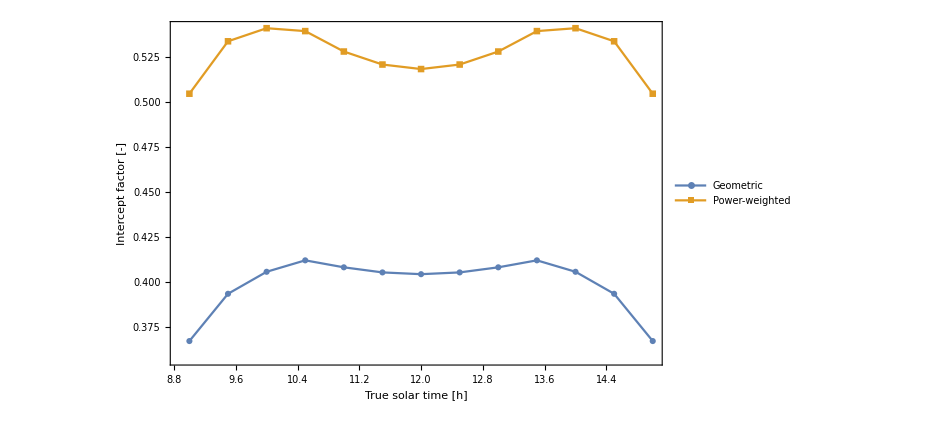

```mathematica
geomSeries=interceptFactorTable/. a_Association:>{a["TST"],a["GeometricInterceptFactor"]};

powerSeries=interceptFactorTable/. a_Association:>{a["TST"],a["PowerWeightedInterceptFactor"]};

ListLinePlot[{geomSeries,powerSeries},Frame->True,FrameLabel->{"True solar time [h]","Intercept factor [-]"},PlotLegends->{"Geometric","Power-weighted"},PlotMarkers->Automatic,ImageSize->700]
```

#### Concentration ratio

Assumes : 
-rayTracingDataAtTST[TST, rayLen] 
- reactorRadius 
- reactorCenterline
 - DNI[TST] - rhoMirror

```mathematica
(*Reactor geometry*)
reactorPoints=reactorCenterline;

segmentLengths=Norm/@Differences[reactorPoints];
totalReactorLength=Total[segmentLengths];

(*Lateral surface area of cylindrical reactor*)
reactorArea=2 Pi reactorRadius totalReactorLength;

(*---------------------------------------------------------------*)
(*Concentration ratio at a given TST*)
(*---------------------------------------------------------------*)
concentrationRatioAtTST[TST_,rayLen_:3.0]:=Module[
{data,hitData,geometricWeights,reflectedPowerPerUnitDNI,C},

data=rayTracingDataAtTST[TST,rayLen];
hitData=Select[data,#["HitQ"]&];

(*Weight proportional to reflected power,but without DNI*)
geometricWeights=(rhoMirror*#["Weight"])&/@hitData;

(*This is P_intercepted/DNI*)
reflectedPowerPerUnitDNI=Total[geometricWeights];

(*Concentration ratio:DNI cancels out*)
C=If[reactorArea>0,
N[reflectedPowerPerUnitDNI/reactorArea],
Indeterminate
];
<|"TST"->TST,"InterceptedPowerOverDNI"->reflectedPowerPerUnitDNI,"ReactorArea"->reactorArea,"ConcentrationRatio"->C|>
];

(*Example*)
concentrationRatioAtTST[12.0,3.0]

(*Time evolution*)
tstSamples=Range[9.0,15.0,0.5];

concentrationTable=concentrationRatioAtTST[#,3.0]&/@tstSamples;

concentrationDataset=Dataset[concentrationTable];
concentrationDataset

(*Summary*)
concentrationSummary=<|"MeanC"->Mean[DeleteCases[concentrationTable[[All,"ConcentrationRatio"]],Indeterminate]],"MinC"->Min[DeleteCases[concentrationTable[[All,"ConcentrationRatio"]],Indeterminate]],"MaxC"->Max[DeleteCases[concentrationTable[[All,"ConcentrationRatio"]],Indeterminate]]|>;

concentrationSummary//Dataset
```

<|TST→12.,InterceptedPowerOverDNI→35.427,ReactorArea→63.9196,ConcentrationRatio→0.554244|>

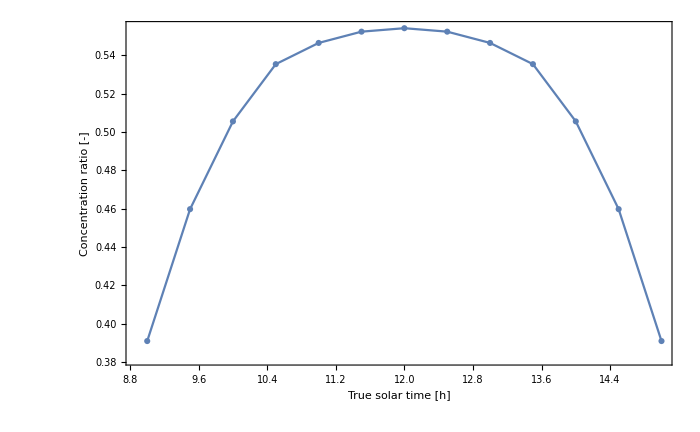

```mathematica
(*---------------------------------------------------------------*)
(*Plot*)
(*---------------------------------------------------------------*)
concSeries=concentrationTable/. a_Association:>{a["TST"],a["ConcentrationRatio"]};

ListLinePlot[concSeries,Frame->True,FrameLabel->{"True solar time [h]","Concentration ratio [-]"},PlotMarkers->Automatic,ImageSize->700]
```

#### UNIFORMITY OF POWER DISTRIBUTION ON THE REACTOR

```mathematica
rhoMirror=0.90; (*A good one*)

(*---------------------------------------------------------------*)
(*Reactor centerline geometry*)
(*---------------------------------------------------------------*)
reactorPoints=reactorCenterline;

segmentLengths=Norm/@Differences[reactorPoints];
arcLengths=Prepend[Accumulate[segmentLengths],0.0];
totalReactorLength=Last[arcLengths];

(*---------------------------------------------------------------*)
(*Utility:check that a point is a valid 3D numeric vector*)
(*---------------------------------------------------------------*)
validPointQ[p_]:=VectorQ[p,NumericQ]&&Length[p]==3;

(*---------------------------------------------------------------*)
(*Curvilinear coordinate of the closest centerline node*)
(*---------------------------------------------------------------*)
nearestArcCoordinate[pt_?validPointQ]:=Module[
{dists,k},
dists=Norm/@((#-pt)&/@reactorPoints);
k=First@Ordering[dists,1];
arcLengths[[k]]];

(*---------------------------------------------------------------*)
(*1D binning along the reactor axis*)
(*---------------------------------------------------------------*)
nBinsUniformity=30;
binEdges=Subdivide[0.0,totalReactorLength,nBinsUniformity];
binCenters=MovingAverage[binEdges,2];
deltaS=Differences[binEdges];

(*Lateral area of each cylindrical strip*)
binAreas=2 Pi reactorRadius deltaS;

(*Rule for nearest-bin assignment*)
binRule=Thread[binCenters->Range[nBinsUniformity]];

(*---------------------------------------------------------------*)
(*Uniformity data at a given TST*)
(*---------------------------------------------------------------*)
uniformityDataAtTST[TST_,rayLen_:3.0]:=Module[{data,hitData,weights,hitPts,sCoords,binIndex,powerBins,qBins,meanQ,stdQ,cvQ,uniformityIndex},data=rayTracingDataAtTST[TST,rayLen];
(*Keep only rays that hit and whose hit point is a valid 3D point*)hitData=Select[data,TrueQ[#["HitQ"]]&&validPointQ[#["HitPoint"]]&];
If[Length[hitData]==0,Return[<|"TST"->TST,"PowerBins"->ConstantArray[0.0,nBinsUniformity],"PowerDensityBins"->ConstantArray[0.0,nBinsUniformity],"MeanPowerDensity"->0.0,"StdPowerDensity"->0.0,"UniformityCV"->Indeterminate,"UniformityIndex"->Indeterminate|>]];
(*Relative reflected power weight per hit patch.DNI is omitted because it is common to all rays at fixed TST and cancels out in the uniformity ratios.*)weights=(rhoMirror*#["Weight"])&/@hitData;
(*Hit points on the reactor*)
hitPts=hitData[[All,"HitPoint"]];
(*Arc coordinate along reactor*)
sCoords=nearestArcCoordinate/@hitPts;
(*Assign each hit to nearest axial bin*)
binIndex=First/@(Nearest[binRule,#]&/@sCoords);
(*Accumulate power per bin*)
powerBins=ConstantArray[0.0,nBinsUniformity];
Do[powerBins[[binIndex[[k]]]]+=weights[[k]],{k,1,Length[weights]}];
(*Local power density*)
qBins=N[powerBins/binAreas];
meanQ=N[Mean[qBins]];
stdQ=N[StandardDeviation[qBins]];
cvQ=If[NumericQ[meanQ]&&meanQ>0,N[stdQ/meanQ],Indeterminate];
uniformityIndex=If[NumericQ[meanQ]&&meanQ>0,N[1-stdQ/meanQ],Indeterminate];
<|"TST"->TST,"PowerBins"->powerBins,"PowerDensityBins"->qBins,"MeanPowerDensity"->meanQ,"StdPowerDensity"->stdQ,"UniformityCV"->cvQ,"UniformityIndex"->uniformityIndex|>];

(*---------------------------------------------------------------*)
(*Example at a single time*)
(*---------------------------------------------------------------*)
uniformityDataAtTST[12.0,3.0]

(*---------------------------------------------------------------*)
(*Table over the operating interval*)
(*---------------------------------------------------------------*)
tstSamples=Range[9.0,15.0,0.5];

uniformityTable=uniformityDataAtTST[#,3.0]&/@tstSamples;

uniformitySummaryTable=uniformityTable[[All,{"TST","MeanPowerDensity","StdPowerDensity","UniformityCV","UniformityIndex"}]];

uniformitySummaryTable//Dataset

(*---------------------------------------------------------------*)
(*Global daily summary*)
(*---------------------------------------------------------------*)
uniformitySummary=<|"MeanUniformityCV"->Mean[DeleteCases[uniformityTable[[All,"UniformityCV"]],Indeterminate]],"MinUniformityCV"->Min[DeleteCases[uniformityTable[[All,"UniformityCV"]],Indeterminate]],"MaxUniformityCV"->Max[DeleteCases[uniformityTable[[All,"UniformityCV"]],Indeterminate]],"MeanUniformityIndex"->Mean[DeleteCases[uniformityTable[[All,"UniformityIndex"]],Indeterminate]],"MinUniformityIndex"->Min[DeleteCases[uniformityTable[[All,"UniformityIndex"]],Indeterminate]],"MaxUniformityIndex"->Max[DeleteCases[uniformityTable[[All,"UniformityIndex"]],Indeterminate]]|>;

uniformitySummary//Dataset
```

<|TST→12.,PowerBins→{0.0309461,0.403275,0.772495,0.729147,0.731922,0.745354,0.766725,0.755235,1.07971,1.30369,2.59113,3.13539,2.83461,4.94767,4.63957,6.84638,4.94767,2.83461,3.13539,2.59113,1.30369,1.07971,0.755235,0.766725,0.745354,0.731922,0.729147,0.772495,0.403275,0.0309461},PowerDensityBins→{0.0145242,0.189273,0.362563,0.342218,0.34352,0.349824,0.359855,0.354462,0.506752,0.611876,1.21612,1.47157,1.3304,2.32214,2.17753,3.21328,2.32214,1.3304,1.47157,1.21612,0.611876,0.506752,0.354462,0.359855,0.349824,0.34352,0.342218,0.362563,0.189273,0.0145242},MeanPowerDensity→0.831366,StdPowerDensity→0.804466,UniformityCV→0.967644,UniformityIndex→0.0323562|>

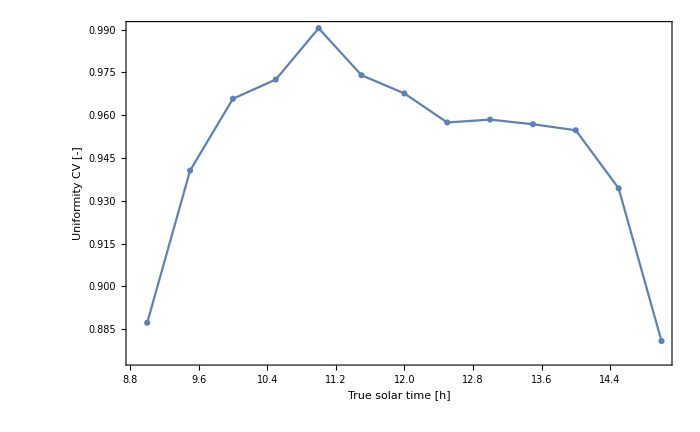

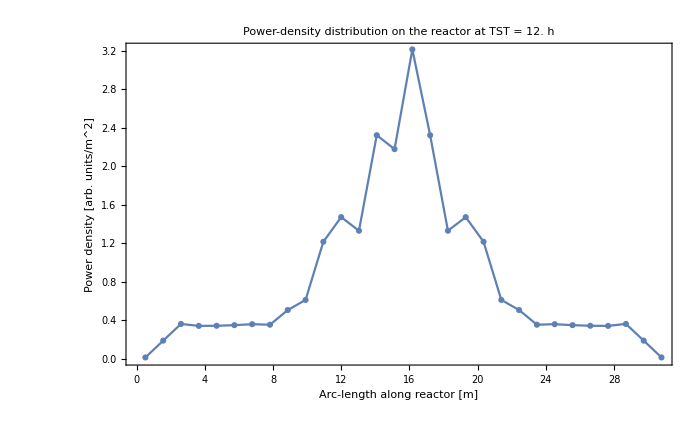

```mathematica
(*---------------------------------------------------------------*)
(*Plot of uniformity vs time*)
(*---------------------------------------------------------------*)
uniformitySeries=uniformityTable/. a_Association:>{a["TST"],a["UniformityCV"]};

ListLinePlot[uniformitySeries,Frame->True,FrameLabel->{"True solar time [h]","Uniformity CV [-]"},PlotMarkers->Automatic,ImageSize->700]

(*---------------------------------------------------------------*)
(*Spatial profile at a selected time*)
(*---------------------------------------------------------------*)
selectedTST=12.0;
selectedUniformity=uniformityDataAtTST[selectedTST,3.0];

spatialSeries=Transpose[{binCenters,selectedUniformity["PowerDensityBins"]}];

ListLinePlot[spatialSeries,Frame->True,FrameLabel->{"Arc-length along reactor [m]","Power density [arb. units/m^2]"},PlotLabel->Row[{"Power-density distribution on the reactor at TST = ",selectedTST," h"}],PlotMarkers->Automatic,ImageSize->700]
```

#### TEMPORAL STABILITY

Assumes that the following have already been computed : -interceptFactorTable - concentrationTable - uniformityTable Each one should be a list of Associations indexed by TST

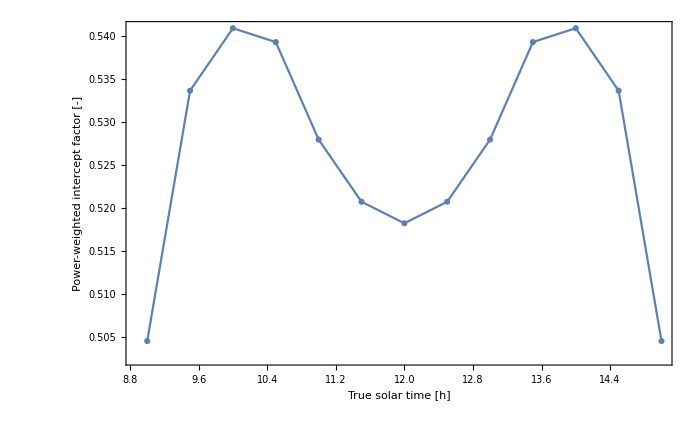

-Graphics-

-Graphics-

```mathematica
(*---------------------------------------------------------------*)(*Helper:temporal stability statistics for a scalar time series*)(*---------------------------------------------------------------*)temporalStats[data_List,key_String]:=Module[{vals,meanVal,minVal,maxVal,rangeAbs,rangeRel,stdVal,cvVal},vals=DeleteCases[data[[All,key]],Indeterminate];
If[Length[vals]==0,Return[<|"Mean"->Indeterminate,"Min"->Indeterminate,"Max"->Indeterminate,"AbsoluteRange"->Indeterminate,"RelativeRange"->Indeterminate,"StdDev"->Indeterminate,"TemporalCV"->Indeterminate|>]];
meanVal=N[Mean[vals]];
minVal=N[Min[vals]];
maxVal=N[Max[vals]];
rangeAbs=N[maxVal-minVal];
rangeRel=If[meanVal!=0,N[(maxVal-minVal)/meanVal],Indeterminate];
stdVal=N[StandardDeviation[vals]];
cvVal=If[meanVal!=0,N[stdVal/meanVal],Indeterminate];
<|"Mean"->meanVal,"Min"->minVal,"Max"->maxVal,"AbsoluteRange"->rangeAbs,"RelativeRange"->rangeRel,"StdDev"->stdVal,"TemporalCV"->cvVal|>];

(*---------------------------------------------------------------*)
(*Temporal stability summary for the main metrics*)
(*---------------------------------------------------------------*)
temporalStabilitySummary=<|"PowerWeightedInterceptFactor"->temporalStats[interceptFactorTable,"PowerWeightedInterceptFactor"],"ConcentrationRatio"->temporalStats[concentrationTable,"ConcentrationRatio"],"UniformityCV"->temporalStats[uniformityTable,"UniformityCV"]|>;

temporalStabilitySummary//Dataset

(*---------------------------------------------------------------*)
(*Optional compact table for the paper*)
(*---------------------------------------------------------------*)
temporalStabilityCompact={<|"Metric"->"Power-weighted intercept factor","Mean"->temporalStabilitySummary["PowerWeightedInterceptFactor","Mean"],"Min"->temporalStabilitySummary["PowerWeightedInterceptFactor","Min"],"Max"->temporalStabilitySummary["PowerWeightedInterceptFactor","Max"],"RelativeRange"->temporalStabilitySummary["PowerWeightedInterceptFactor","RelativeRange"],"TemporalCV"->temporalStabilitySummary["PowerWeightedInterceptFactor","TemporalCV"]|>,<|"Metric"->"Concentration ratio","Mean"->temporalStabilitySummary["ConcentrationRatio","Mean"],"Min"->temporalStabilitySummary["ConcentrationRatio","Min"],"Max"->temporalStabilitySummary["ConcentrationRatio","Max"],"RelativeRange"->temporalStabilitySummary["ConcentrationRatio","RelativeRange"],"TemporalCV"->temporalStabilitySummary["ConcentrationRatio","TemporalCV"]|>,<|"Metric"->"Uniformity CV","Mean"->temporalStabilitySummary["UniformityCV","Mean"],"Min"->temporalStabilitySummary["UniformityCV","Min"],"Max"->temporalStabilitySummary["UniformityCV","Max"],"RelativeRange"->temporalStabilitySummary["UniformityCV","RelativeRange"],"TemporalCV"->temporalStabilitySummary["UniformityCV","TemporalCV"]|>};

temporalStabilityCompact//Dataset

(*---------------------------------------------------------------*)
(*Time-series plots*)
(*---------------------------------------------------------------*)
ifSeries=interceptFactorTable/. a_Association:>{a["TST"],a["PowerWeightedInterceptFactor"]};
concSeries=concentrationTable/. a_Association:>{a["TST"],a["ConcentrationRatio"]};
uniSeries=uniformityTable/. a_Association:>{a["TST"],a["UniformityCV"]};

ListLinePlot[ifSeries,Frame->True,FrameLabel->{"True solar time [h]","Power-weighted intercept factor [-]"},PlotMarkers->Automatic,ImageSize->700]

ListLinePlot[concSeries,Frame->True,FrameLabel->{"True solar time [h]","Concentration ratio [-]"},PlotMarkers->Automatic,ImageSize->700]

ListLinePlot[uniSeries,Frame->True,FrameLabel->{"True solar time [h]","Uniformity CV [-]"},PlotMarkers->Automatic,ImageSize->700]
```

### SENSITIVITY ANALYSIS

This block assumes that the following already exist :
 	  -surfaceGrid 
	  - nCurves, nPts 
 	  - normalAt[i, j] 
	  - patchAreaAt[i, j] 
	  - firstTubeHit[p, r, rayLen] 
	  - h[dn, TST], azimuth[dn, TST] 
	  - reactorCenterline, reactorRadius 
	  - rhoMirror 
	  - concentrationRatioAtTST 
	  - interceptFactorAtTST 
	  - uniformityDataAtTST

```mathematica
(*---------------------------------------------------------------*)
(*Utilities*)
(*---------------------------------------------------------------*)validPointQ[p_]:=VectorQ[p,NumericQ]&&Length[p]==3;

incidentDirection3D[TST_]:=Normalize[
{
   Cos[h[dn,TST]] Cos[azimuth[dn,TST]],
-Cos[h[dn,TST]] Sin[azimuth[dn,TST]],
-Sin[h[dn,TST]]}];

(*Random unit vector*)
randomUnitVector[]:=Normalize[RandomVariate[NormalDistribution[0,1],3]];

(*Small random rotation of a vector by angular std sigmaAngle*)
perturbDirection[v_,sigmaAngle_]:=Module[
{axis,angle},
axis=randomUnitVector[];
angle=RandomVariate[NormalDistribution[0,sigmaAngle]];
Normalize[RotationTransform[angle,axis][v]]
];

(*Small random displacement of a point by std sigmaPos*)
perturbPoint[p_,sigmaPos_]:=p+RandomVariate[NormalDistribution[0,sigmaPos],3];

(*---------------------------------------------------------------*)
(*Perturbed ray-tracing data*)
(*---------------------------------------------------------------*)
rayTracingDataAtTSTPerturbed[TST_,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[{sBase,s,data,p,pPert,n,nPert,cosInc,r,hit,area},

sBase=incidentDirection3D[TST];
s=If[sigmaSolar>0,perturbDirection[sBase,sigmaSolar],sBase];

data=Reap[
Do[
p=surfaceGrid[[i,j]];
pPert=If[sigmaPos>0,perturbPoint[p,sigmaPos],p];

n=normalAt[i,j];
nPert=If[sigmaNormal>0,perturbDirection[n,sigmaNormal],n];

cosInc=-s.nPert;

If[cosInc>0,
r=Normalize[s-2 (s.nPert) nPert];
hit=firstTubeHit[pPert,r,rayLen];
area=patchAreaAt[i,j];

Sow[<|"i"->i,"j"->j,"Point"->pPert,"Normal"->nPert,"CosInc"->cosInc,"PatchArea"->area,"Weight"->cosInc*area,"ReflectedDirection"->r,"HitPoint"->hit,"HitQ"->(hit=!=Nothing)|>
];
],
{i,1,nCurves},{j,1,nPts}
]][[2,1]];
data
];

(*---------------------------------------------------------------*)
(*Perturbed intercept factor*)
(*---------------------------------------------------------------*)
interceptFactorAtTSTPerturbed[TST_,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[
{data,nIll,nHit,geomIF,totalWeight,hitWeight,powerIF},

data=rayTracingDataAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];

nIll=Length[data];
nHit=Count[data[[All,"HitQ"]],True];

geomIF=If[nIll>0,N[nHit/nIll],Indeterminate];
totalWeight=Total[data[[All,"Weight"]]];
hitWeight=Total[Cases[data,a_/;TrueQ[a["HitQ"]]:>a["Weight"]]];
powerIF=If[totalWeight>0,N[hitWeight/totalWeight],Indeterminate];

<|"TST"->TST,"GeometricInterceptFactor"->geomIF,"PowerWeightedInterceptFactor"->powerIF|>
];

(*---------------------------------------------------------------*)
(*Perturbed concentration ratio*)
(*---------------------------------------------------------------*)
concentrationRatioAtTSTPerturbed[TST_,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[
{data,hitData,effectiveArea,C},

data=rayTracingDataAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];
hitData=Select[data,TrueQ[#["HitQ"]]&];

effectiveArea=Total[(rhoMirror*#["Weight"])&/@hitData];

C=If[reactorArea>0,N[effectiveArea/reactorArea],Indeterminate];
<|"TST"->TST,"ConcentrationRatio"->C|>
];

(*---------------------------------------------------------------*)
(*Perturbed uniformity*)
(*Reuses nearestArcCoordinate,binCenters,binAreas,etc.*)
(*---------------------------------------------------------------*)
uniformityDataAtTSTPerturbed[TST_,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[
{data,hitData,weights,hitPts,sCoords,binRule,binIndex,powerBins,qBins,meanQ,stdQ,cvQ,uniformityIndex},

data=rayTracingDataAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];
hitData=Select[data,TrueQ[#["HitQ"]]&&validPointQ[#["HitPoint"]]&];

If[Length[hitData]==0,Return[<|"TST"->TST,"UniformityCV"->Indeterminate,"UniformityIndex"->Indeterminate|>]
];

weights=(rhoMirror*#["Weight"])&/@hitData;
hitPts=hitData[[All,"HitPoint"]];
sCoords=nearestArcCoordinate/@hitPts;

binRule=Thread[binCenters->Range[nBinsUniformity]];
binIndex=First/@(Nearest[binRule,#]&/@sCoords);

powerBins=ConstantArray[0.0,nBinsUniformity];
Do[
powerBins[[binIndex[[k]]]]+=weights[[k]],
{k,1,Length[weights]}
];

qBins=N[powerBins/binAreas];
meanQ=N[Mean[qBins]];
stdQ=N[StandardDeviation[qBins]];

cvQ=If[NumericQ[meanQ]&&meanQ>0,N[stdQ/meanQ],Indeterminate];
uniformityIndex=If[NumericQ[meanQ]&&meanQ>0,N[1-stdQ/meanQ],Indeterminate];

<|"TST"->TST,"UniformityCV"->cvQ,"UniformityIndex"->uniformityIndex|>
];

(*---------------------------------------------------------------*)
(*One Monte Carlo realization*)
(*---------------------------------------------------------------*)
sensitivitySample[TST_,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[
{ifData,cData,uData},

ifData=interceptFactorAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];
cData=concentrationRatioAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];
uData=uniformityDataAtTSTPerturbed[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar];

<|"TST"->TST,"SigmaPosition"->sigmaPos,"SigmaNormal"->sigmaNormal,"SigmaSolar"->sigmaSolar,"PowerWeightedInterceptFactor"->ifData["PowerWeightedInterceptFactor"],"ConcentrationRatio"->cData["ConcentrationRatio"],"UniformityCV"->uData["UniformityCV"]|>
];

(*---------------------------------------------------------------*)
(*Monte Carlo study for a given perturbation scenario*)
(*---------------------------------------------------------------*)
sensitivityStudy[TST_,nRuns_:20,rayLen_:3.0,sigmaPos_:0.0,sigmaNormal_:0.0,sigmaSolar_:0.0]:=Module[
{baseIF,baseC,baseU,samples,ifVals,cVals,uVals},

baseIF=interceptFactorAtTST[TST,rayLen]["PowerWeightedInterceptFactor"];
baseC=concentrationRatioAtTST[TST,rayLen]["ConcentrationRatio"];
baseU=uniformityDataAtTST[TST,rayLen]["UniformityCV"];

samples=Table[
sensitivitySample[TST,rayLen,sigmaPos,sigmaNormal,sigmaSolar],
{nRuns}
];

ifVals=DeleteCases[samples[[All,"PowerWeightedInterceptFactor"]],Indeterminate];
cVals=DeleteCases[samples[[All,"ConcentrationRatio"]],Indeterminate];
uVals=DeleteCases[samples[[All,"UniformityCV"]],Indeterminate];

<|"Scenario"-><|"TST"->TST,"Runs"->nRuns,"SigmaPosition"->sigmaPos,"SigmaNormal"->sigmaNormal,"SigmaSolar"->sigmaSolar|>,

"PowerWeightedInterceptFactor"-><|"Base"->baseIF,"MeanPerturbed"->Mean[ifVals],"MinPerturbed"->Min[ifVals],"MaxPerturbed"->Max[ifVals],"RelativeLossMean"->If[baseIF>0,N[(baseIF-Mean[ifVals])/baseIF],Indeterminate]|>,

"ConcentrationRatio"-><|"Base"->baseC,"MeanPerturbed"->Mean[cVals],"MinPerturbed"->Min[cVals],"MaxPerturbed"->Max[cVals],"RelativeLossMean"->If[baseC>0,N[(baseC-Mean[cVals])/baseC],Indeterminate]|>,

"UniformityCV"-><|"Base"->baseU,"MeanPerturbed"->Mean[uVals],"MinPerturbed"->Min[uVals],"MaxPerturbed"->Max[uVals],"RelativeChangeMean"->If[baseU=!=0&&NumericQ[baseU],N[(Mean[uVals]-baseU)/baseU],Indeterminate]|>,

"Samples"->samples|>
];

(* ================================================================*)
(*EXAMPLES OF SCENARIOS*)
(* ================================================================*)

(*1 mm construction tolerance,0.5 degree normal error,0 solar spread*)
scenario1=sensitivityStudy[12.0,20,3.0,0.001,(*meters*)0.5 Degree,(*radians*)0.0];

scenario1//Dataset

(*5 mm construction tolerance,1 degree normal error*)
scenario2=sensitivityStudy[12.0,20,3.0,0.005,1.0 Degree,0.0];

scenario2//Dataset

(*5 mm+1 degree+0.25 degree solar spread*)
scenario3=sensitivityStudy[12.0,20,3.0,0.005,1.0 Degree,0.25 Degree];

scenario3//Dataset
```